## General Functions

This file was created with Mathematica/10.2

Prior to analysis you must :
(1) Run the simulations (see versatile_framework_paper/README.md)
(2) Postprocess: 
In most cases this means converting the human-readable-output of the simulation to something easier for mathematica to read. My solution was a “dat” file. The python script versatile_framework_paper/python/txt2dat.py converts the txt files from the simulation output to dat files that mathematica can import easily using the pts function, below.
Example Usage:
python versatile_framework_paper/python/txt2dat.py test actins
generates the file test/txt_stack/actins.dat from the file test/txt_stack/actins.txt. 
For Cytosim trajectories, there’s a similar command
python versatile_framework_paper/python/cs_txt2dat.py test 
to produce the “objects.dat” file
For most of the analyses below, this must be done for the links file and sometimes the actins file. 

For figures 2, 3D, 7C-D and S3 there are separate pre/post processing requirements; see there for details.

```mathematica
Import["~/Code/cytomod/versatile_framework_paper/mathematica/cytomod_functions.m"];
```

### Directory Setup

```mathematica
outdir="/project/weare-dinner/simonfreedman/cytomod/out";
vfdir=outdir<>"/vf_r2";
figdir=vfdir<>"/figs";
fig1dir=outdir<>"/minimal_actomyosin/";
fig2dir=vfdir<>"/profiling/koff1_kend10/";
fig3dir=vfdir<>"/pl/";
fig3Cdir="/scratch/midway2/simonfreedman/cytomod/out/vf_r2/3C/";
fig5dir=vfdir<>"/shear/shear_xy75_koff0.1/kf1000/";
fig6dir=vfdir<>"/testing/afines_low_rc";

fig7dir=vfdir<>"/contracting/mdens0.2_xldens1/mkoff0.1_mkend1";
figS3dir=vfdir<>"/contracting/mdens1_xldens1";

figS2dir=vfdir<>"/shear/nbw_arr";

csoutdir="/project/weare-dinner/simonfreedman/cytosim/out";
figS4dir=csoutdir<>"/pl";
figS5dir=csoutdir<>"/vf_r2/motility";
```

## Figure 1

### D

Requires first running 
	txt2dat.py [fig1dir <> "/slide/"] links
	txt2dat.py [fig1dir <> "/slide/"] amotors

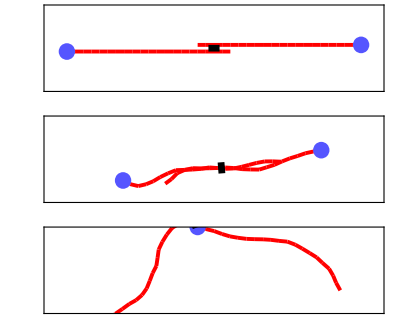

```mathematica
dir=fig1dir<>"/slide";
lks=pts[dir,"links"];
amots=pts[dir,"amotors"];
fs=draw[{},lks,amots,{},dir,False,{20,5},True, 21,Red,"movie",-1,1];
GraphicsColumn[fs[[{1,31,101}]],Spacings->10]
```

### E

Requires first running 
	txt2dat.py [fig1dir <> "/buckle/"] links
	txt2dat.py [fig1dir <> "/buckle/"] amotors
	txt2dat.py [fig1dir <> “/buckle/”] pmotors

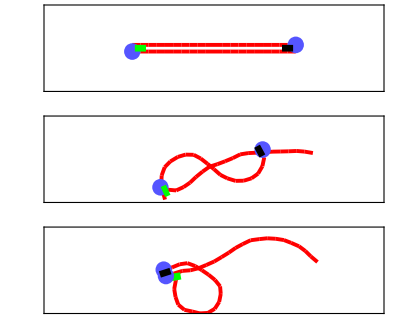

```mathematica
dir=fig1dir<>"/buckle";
lks=pts[dir,"links"];
amots=pts[dir,"amotors"];
pmots=pts[dir,"pmotors"];
fs=draw[{},lks,amots,pmots,dir,False,{20,5},True, 21,Red,"movie",-1,1];
GraphicsColumn[fs[[{1,31,101}]],Spacings->10]
```

## Figure 2

For these plots, you have to measure the wall clock time of the simulation. I did this with the following Bash script, where $cmd was my simulation command (see versatile_framework_paper/README.md) and $data_dr was the “data” output directory of the simulation

startt = `date + % s`
./$cmd
endt = `date + % s`
tott = $ (echo $startt $endt | awk' {printf "%d", $2 - $1}')
echo $tott > "$data_dr/time.txt"

### A

```mathematica
nfil0=20;
nm0=11;
ρ0=0.1;
area=50^2;
```

#### Red Curve

```mathematica
dir=fig2dir<>"/2A/npoly_arr";
ns=Sort[Flatten[Outer[Times,{1,2,5},10^Range[0,3]]]];
dirs=Table[dir<>"/dens"<>ToString[n],{n,ns}];
times=Flatten[Table[Import[dr<>"/data/time.txt","TSV"],{dr,dirs}]];
nparts=ns nm0+4ρ0 area;(*in paper, constant addition was off -- 4*0.1*75^2"*)
reddat={nparts,times}ᵀ;
```

#### Blue Curve

```mathematica
dir=fig2dir<>"/2A/mdens_arr";
ns=Sort[Flatten[Outer[Times,{1,2,5},10^Range[0,4]]]];
denss=ns*0.001;
dirs=Table[dir<>"/dens"<>ToString[NumberForm[d,{3,3}]],{d,denss}];
times=Flatten[Table[Import[dr<>"/data/time.txt","TSV"],{dr,dirs}]];
nparts=nfil0 nm0+2ρ0 area + 2 denss area;
bluedat={nparts,times}ᵀ;
```

#### Black Curve

```mathematica
dir=fig2dir<>"/2A/dens_arr";
ns=Sort[Join[Flatten[Outer[Times,{1,2,5},10^Range[0,2]]],{1000,2000}]];
dirs=Table[dir<>"/dens"<>ToString[n],{n,ns}];
times=Flatten[Table[Import[dr<>"/data/time.txt","TSV"],{dr,dirs}]];
nparts=ns nm0+4 ρ0 ns/nfil0 area;
blackdat={nparts,times}ᵀ;
```

```mathematica
ticksb=LogTicks[10,2,6];
tickst=LogTicks[10,2,6,ShowTickLabels->False];
ticksl=LogTicks[10,0,10];
ticksr=LogTicks[10,0,10,ShowTickLabels->False];
```

```mathematica
npartplt=Show[
ListPlot[
{Log10[reddat[[4;;]]],Log10[bluedat[[6;;]]],Log10[blackdat[[4;;]]]},
PlotMarkers->{●,10},PlotStyle->{Red,Blue,Black},Joined->True,
FrameTicks->{{ticksl,ticksr},{ticksb,tickst}},
PlotRange->{{2.7,5.55},{0,5.2}},FrameLabel->{"# Particles","Wall Clock Time (s)"},
PlotLegends->Placed[PointLegend[{"ρ_motor const.","ρ_actin const."},LabelStyle->FontSize->18,LegendMarkerSize->{30,30},Spacings->0.1],{0.7,0.2}]],
Plot[{x-2.3,2x-4.7},{x,1,7},PlotStyle->{{Blue,Thick,Dashed},{Black,Thick,Dashed}}]];
```

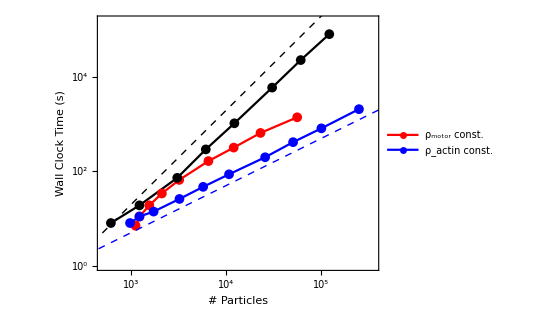

```mathematica
npartplt
```

### B

```mathematica
ticksl=LogTicks[10,0,4];
ticksr=LogTicks[10,0,4,ShowTickLabels->False];
yrng={0.1,3.2};
flabel={"System Size (μm^2)","Wall Clock Time (s)","Grid Density (μm^-2)"};
```

#### blue curve

```mathematica
dir=fig2dir<>"/sys_size_arr";
ns=10Range[10];
dirs=Table[dir<>"/sz"<>ToString[n],{n,ns}];
times=Flatten[Table[Import[dr<>"/data/time.txt","TSV"],{dr,dirs}]];
szs=ns^2;
bluedat={szs,times}ᵀ;
```

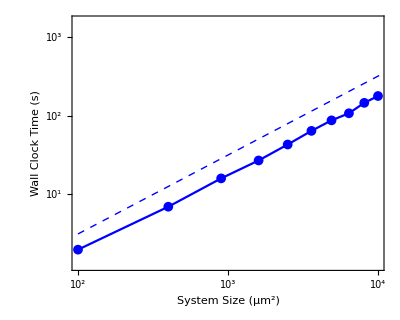

```mathematica
ticksb=LogTicks[10,1,5,TickLabelStep->0.25];
tickst=LogTicks[10,1,5,ShowTickLabels->False];
szplt=Show[ListPlot[Log10[bluedat],PlotMarkers->{●,10},Axes->False,
PlotStyle->Blue,Joined->True,
FrameTicks->{{ticksl,ticksr},{ticksb,ticksb}},
FrameStyle->{{Black,Black},{Blue,White}},
PlotRange->{Automatic,yrng},
FrameLabel->flabel],
Plot[{x-1.5},{x,2,5},PlotStyle->{Blue,Thick,Dashed}]]
```

#### red curve

```mathematica
dir=fig2dir<>"/grid_factor/";
ns=Join[Range[0,10,2],10Range[10],Range[150,500,50]];
gfs=ns*0.01;
dirs=Table[dir<>"gf"<>ToString[NumberForm[gf,{1,2}]],{gf,gfs}];
times=Flatten[Table[Import[dr<>"/data/time.txt","TSV"],{dr,dirs}]];
reddat={gfs^2,times}ᵀ;
```

```mathematica
tickst=LogTicks[10,-3,3,TickLabelStep->0.25];
gfplt=Show[ListPlot[Log10[reddat],PlotMarkers->{●,10},Axes->False,
PlotStyle->Red,Joined->True,
FrameTicks->{{ticksl,ticksr},{tickst,tickst}},
FrameStyle->{{Black,Black},{White,Red}},
Frame->{{False,False},{False,True}},
PlotRange->{Full,yrng},
FrameLabel->flabel],
Plot[-x+0.3,{x,-2.6,-0.5},PlotStyle->{{Red,Thick,Dashed},{Blue,Thick,Dashed}}]]
```

```mathematica
Manipulate[Overlay[{szplt,Show[gfplt,ImageSize->s1]},Alignment->{x1,y1}],{s1,100,400},{x1,-1,1},{y1,-1,1}]
```

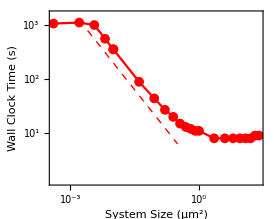
-Graphics--Graphics-

```mathematica
gfszplt=Overlay[{szplt,Show[gfplt,ImageSize->274]},Alignment->{0.72,1}]
```

```mathematica
Export[figdir<>"/2BC.eps",gfplt];
```

## Figures 3, S2

### 3 B

```mathematica
dx=1;
L=20;
nfils=20;
nlks=L/dx;
teq=100;
lp=17;
```

```mathematica
fig3Adir=fig3dir<>"/kl_arr/kl1.00";
lks=Partition[#,nlks]&/@pts[fig3Adir,"links"];
angs=ParallelMap[anglesT,lks,{2}];
angsbw=ParallelMap[anglesBwT,angs,{2}];
ccfs=ParallelMap[ccf,angsbw,{2}];
th2s=ParallelMap[th2,angsbw,{2}];
```

```mathematica
muths=Mean[th2s[[teq;;]]];
muthsmu=Mean[muths];
muthserr=StandardDeviation[muths]/Sqrt[Length[muths]];
```

```mathematica
muccfs=Mean[ccfs[[teq;;]]];
muccfsmu=Mean[muccfs];
muccfserr=StandardDeviation[muccfs]/Sqrt[Length[muccfs]];
```

```mathematica
xs=Range[dx,L-dx,dx];
```

```mathematica
th2plt=Show[
ListPlot[{
{xs,muthsmu}ᵀ,
{xs,muthsmu-muthserr}ᵀ,
{xs,muthsmu+muthserr}ᵀ},
FrameLabel->{"","","",Rotate[Style["⟨θ^2(ℓ)⟩",Blue],Pi]},
FrameStyle->Blue,
Frame->{{False,True},{False,False}},
FrameTicks->{{None,All},{None,None}},
(*Comment out next three lines if you don't want joined*)
(**)
(*PlotStyle->{Blue,{Blue,Opacity[0.01]},{Blue,Opacity[0.01]}},
PlotMarkers->{{●,10},{○,0.01},{○,0.01},{●,5},{○,0.01},{○,0.01}},
Joined->{False,True,True},*)
(**)
(*Uncomment next four line if you don't want joined*)

FillingStyle->Directive[Opacity[1],Thickness[0.003]],
PlotMarkers->{{●,12},"+","+"},
PlotStyle->Blue,
Joined->False,

Filling->{2->{3}},
PlotRange->{{0,20},Automatic}
],
Plot[{x/(lp)},{x,0,50},PlotStyle->{Thick,Dashing[Large],Blue}]
];
```

```mathematica
ccfplt=Show[
ListLogPlot[{
{xs,muccfsmu}ᵀ,
{xs,muccfsmu-muccfserr}ᵀ,
{xs,muccfsmu+muccfserr}ᵀ},
FrameLabel->{"ℓ (μm)",Style["⟨cosθ(ℓ)⟩",Red]},
FrameStyle->{{Red,Automatic},{Black,Black}},
Frame->{{True,False},{True,True}},
FrameTicks->{{All,None},{All,Automatic}},
(*Comment out next three lines if you don't want joined*)
(**)
(*PlotStyle->{Red,{Red,Opacity[0.01]},{Red,Opacity[0.01]}},
PlotMarkers->{{●,10},{○,0.01},{○,0.01},{●,5},{○,0.01},{○,0.01}},
Joined->{False,True,True},
*)(**)
(*Uncomment next four line if you don't want joined*)
(**)
FillingStyle->Directive[Opacity[1],Thickness[0.003]],
PlotMarkers->{{●,12},"+","+"},
PlotStyle->Red,
Joined->False,
(**)
Filling->{2->{3}},
PlotRange->{{0,20},Automatic}],
LogPlot[{Exp[-x/(2lp)]},{x,0,50},PlotStyle->{Thick,Dashing[Large],Red}]
];
```

```mathematica
GraphicsRow[{ccfplt,th2plt}]
```

-Graphics-

```mathematica
Export[figdir<>"/3BRed_stderr_joined.pdf",ccfplt];
Export[figdir<>"/3BBlue_stderr_joined.pdf",th2plt];
```

### S2

```mathematica
dir=fig3dir<>"/decor";
lks=pts[dir,"links"];
angs=anglesT/@lks;
angsbw=anglesBwT/@angs;
ccs=Table[CorrelationFunction[angsbw[[All,i]],{0,19999}],{i,1,Length[angsbw[[1]]]}];
mccs=Mean[ccs];
cf={0.005(Range[Length[mccs]]-1),mccs}ᵀ;
decortimes=0.01Table[Total[mccs[[1;;i]]],{i,2,20000}];
```

#### S1A

```mathematica
ps=Join[Range[1,5],Range[7,15,2],Range[20,100,20],Range[150,2000,50]];
```

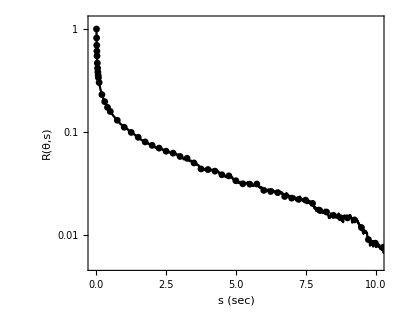

```mathematica
plta=Show[ListLogPlot[cf,PlotRange->{{-0.1,10.1},{0.005,1.2}},Joined->True,PlotStyle->Black,FrameLabel->{"s  (sec)",Style["R(θ,s)",SingleLetterItalics->False]}],
ListLogPlot[cf[[ps]],PlotRange->Full,PlotMarkers->{●,7},PlotStyle->Black]]
```

```mathematica
Export[figdir<>"/S1A.eps",plta];
```

#### S1B

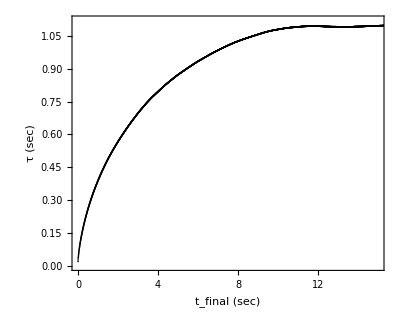

```mathematica
pltb=ListPlot[decortimes, PlotRange->{{0,15},{0,1.12}},PlotStyle->{Black,Thick},DataRange->{0,100},FrameLabel->{"t_final (sec)","τ (sec)"}]
```

```mathematica
Export[figdir<>"/S1B.eps",pltb];
```

### 3 C

```mathematica
seeds=Range[1,1000];
dirs=Table[fig3Cdir<>"seed"<>ToString[s],{s,seeds}];
nfils=100;
tf=2001;
```

#### Evaluate the eigenvalues for the first time

```mathematica
fstreams=OpenRead[#<>"/txt_stack/actins_ext.dat"]&/@dirs;
evs={};
Do[
actsextt=Table[readline3[f,2*nfils],{f,fstreams}];
AppendTo[evs,Table[Eigenvalues[Covariance[actsextt[[All,i,1;;2]]]],{i,2*nfils}]];,
{tf}
];
Export[fig3Cdir<>"/all_evs.dat",evs];
```

#### Import Previously evaluated eigenvalues

```mathematica
evs=ToExpression[Import[fig3Ddir<>"/all_evs.dat","TSV"]];
```

```mathematica
ts=Range[0.001,tf*0.001,0.001];
maxevs=evs[[All,All,1]];
minevs=evs[[All,All,2]];
mumaxevs=Mean/@maxevs;
muminevs=Mean/@minevs;
errmaxevs=(StandardDeviation/@maxevs)/Sqrt[Dimensions[evs][[2]]];
errminevs=(StandardDeviation/@minevs)/Sqrt[Dimensions[evs][[2]]];
```

```mathematica
maxmaxevs=Max/@maxevs;
maxminevs=Max/@minevs;
minmaxevs=Min/@maxevs;
minminevs=Min/@minevs;
```

```mathematica
maxnorm=mumaxevs[[1000]];
minnorm=muminevs[[1000]];
```

```mathematica
idxs=Union[Round[10^Range[Log10[2],Log10[2000],0.05]]];
```

```mathematica
ticksx=LogTicks[10,-3,1];
fluctplt=Show[
ListPlot[Log10[{
{ts,mumaxevs/maxnorm}ᵀ[[idxs]],
{ts,(mumaxevs-errmaxevs)/maxnorm}ᵀ[[idxs]],
{ts,(mumaxevs+errmaxevs)/maxnorm}ᵀ[[idxs]],
{ts,muminevs/minnorm}ᵀ[[idxs]],
{ts,(muminevs-errminevs)/minnorm}ᵀ[[idxs]],
{ts,(muminevs+errminevs)/minnorm}ᵀ[[idxs]]
}],
PlotRange->{{-2.5,Log10[1.2]},{-2.5,0.8}},
PlotStyle->{Blue,{Blue,Opacity[0.1]},{Blue,Opacity[0.1]},Red,{Red,Opacity[0.1]},{Red,Opacity[0.1]}},
PlotMarkers->{{●,7},{○,0.01},{○,0.01},{●,7},{○,0.01},{○,0.01}},
Filling->{2->{3},5->{6}},
FrameLabel->{"t (s)","λ(t)/λ(1)"},
FrameTicks->{{ticksx,Automatic},{ticksx,Automatic}},Joined->{False,True,True,False,True,True},Axes->None
],
LogLogPlot[{t^{7/8},1.05t^{0.75}},{t,0.001,10},PlotStyle->{{Blue,Thick,Dashed},{Red,Thick,Dashed}}]
];
```

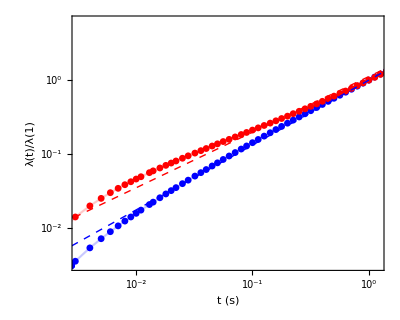

```mathematica
fluctplt
```

```mathematica
Export[figdir<>"/3C.eps",fluctplt];
```

## Figure 4

```mathematica
nlks=20;
dx=1;
L=20;
teq=100;
nfils=20;
teq=100;
Lp=17;
maxl=5;

ticksx=LogTicks[10,-7,3];
rngy={15.9,18.1};
```

### A

```mathematica
kbdir=fig3dir<>"/kb_arr";
kbs={0.005,0.01,0.02,0.05,0.1,0.2,0.5,1.0,2.0,5,10,20,50,100,200,500,1000};
kbdirs=kbdir<>"/kb"<>ToString[NumberForm[#,{1,3},ExponentFunction->(Null&)]]&/@kbs;
```

```mathematica
lks=ParallelTable[Partition[#,nlks]&/@(pts[kbdirs[[i]],"links"][[teq;;-2;;2]]),{i,Length[kbs]}];
lps=ParallelTable[Table[plMeanThsq[lks[[i,All,j,All,3;;4]],dx,L,maxl],{j,Length[lks[[i,1]]]}],{i,Length[lks]}];
lpmeans=Mean/@lps;
lperrs=(StandardDeviation/@lps)/Sqrt[nfils];
```

```mathematica
lplpplt=Show[
ListLogLogPlot[
{{kbs/0.004,lpmeans}ᵀ(*,
{kbs/0.004,lpmeans-lperrs}ᵀ,
{kbs/0.004,lpmeans+lperrs}ᵀ*)
},
PlotMarkers->{{●,10},"+","+"},
PlotStyle->{Black,Red,Red},
Joined->False,
Filling->{{2->{3}},{5->{6}}},
FillingStyle->Directive[Opacity[1],Thickness[0.01]]
],
LogLogPlot[x,{x,0.1,10^6},PlotStyle->{Black,Dashing[0.02](*,Thick*)}],
FrameLabel->{"κ_B (k_BT×μm)","L_p(μm)"}];
```

```mathematica
lplpplt
```

```mathematica
Export[figdir<>"/4A_dt2.eps",lplpplt];
```

### B

```mathematica
kldir=fig3dir<>"/kl_arr/";
kls={0.01,0.02,0.05,0.1,0.2,0.5,1.0,2,5,10,20,50,100,200(*,500,1000*)};
kldirs=kldir<>"/kl"<>ToString[NumberForm[#,{2,2},ExponentFunction->(Null&)]]&/@kls;
```

```mathematica
lks=ParallelTable[Partition[#,nlks]&/@(pts[kldirs[[i]],"links"][[teq;;-1]]),{i,Length[kls]}];
lps=ParallelTable[Table[plMeanThsq[lks[[i,All,j,All,3;;4]],dx,L,maxl],{j,Length[lks[[i,1]]]}],{i,Length[lks]}];
lpmeans=Mean/@lps;
lperrs=(StandardDeviation/@lps)/Sqrt[nfils];
```

```mathematica
kllpplt=Show[
ListPlot[
{{Log10[kls],lpmeans}ᵀ,
{Log10[kls],lpmeans-lperrs}ᵀ,
{Log10[kls],lpmeans+lperrs}ᵀ
},
PlotMarkers->{{●,10},"+","+"},
PlotStyle->{Black,Red,Red},
PlotRange->{Automatic,rngy},
Joined->False,
Filling->{{2->{3}},{5->{6}}},
FillingStyle->Directive[Opacity[1],Thickness[0.01]],
Axes->False,
FrameTicks->{{Automatic,Automatic},{ticksx,Automatic}}
],
Plot[Lp,{x,-3,4},PlotStyle->{Black,Dashing[0.02](*,Thick*)}],
FrameLabel->{"k_a (pN/μm)","L_p(μm)"}];
```

```mathematica
kllpplt
```

```mathematica
Export[figdir<>"/4B.pdf",kllpplt];
```

### C

```mathematica
dxdir=vfdir<>"/pl/dx_arr_kldx1/";
dxs={0.08,0.1,0.2,0.25,0.4,0.5,0.8,1,2,2.5,5};
Ls=nlks*dxs;
dxdirs=dxdir<>"/dx"<>ToString[NumberForm[#,{2,2},ExponentFunction->(Null&)]]&/@dxs;
lks=ParallelTable[Partition[#,nlks]&/@(pts[dxdirs[[i]],"links"][[teq;;-2;;2]]),{i,Length[dxs]}];
lps=ParallelTable[Table[plMeanThsq[lks[[i,All,j,All,3;;4]],dxs[[i]],Ls[[i]],maxl],{j,Length[lks[[i,1]]]}],{i,Length[lks]}];;
lpmeans=Mean/@lps;
lperrs=(StandardDeviation/@lps)/Sqrt[nfils];
```

```mathematica
dxlpplt=Show[
ListLogLinearPlot[
{{dxs,lpmeans}ᵀ,
{dxs,lpmeans-lperrs}ᵀ,
{dxs,lpmeans+lperrs}ᵀ
},
PlotMarkers->{{●,10},"+","+"},
PlotStyle->{Black,Red,Red},
PlotRange->{{0.09,1.2},rngy},
Joined->False,
Filling->{{2->{3}},{5->{6}}},
FillingStyle->Directive[Opacity[1],Thickness[0.01]]
],
LogLinearPlot[Lp,{x,0.001,10000},PlotStyle->{Black,Dashing[0.02]}],
FrameLabel->{"l_a (μm)","L_p(μm)"}];
```

```mathematica
dxlpplt
```

```mathematica
Export[figdir<>"/4C_dt2.pdf",dxlpplt];
```

### D

```mathematica
dtdir=fig3dir<>"/dt_arr/";
dts={(*1,2,5,*)10,20,50,100,200,500,1000,2000,5000,10000,20000,50000}*10.^(-7);
dtdirs=dtdir<>"/dt"<>ToString[NumberForm[#,{1,7},ExponentFunction->(Null&)]]&/@dts;
```

```mathematica
lks=Table[Partition[#,nlks]&/@(pts[dtdirs[[i]],"links"][[teq;;-1;;1]]),{i,Length[dts]}];
lps=Table[Table[plMeanThsq[lks[[i,All,j,All,3;;4]],dx,L,maxl],{j,Length[lks[[i,1]]]}],{i,Length[lks]}];
lpmeans=Mean/@lps;
lperrs=(StandardDeviation/@lps)/Sqrt[nfils];
```

```mathematica
dtlpplt=Show[
ListPlot[
{{Log10[dts],lpmeans}ᵀ,
{Log10[dts],lpmeans-lperrs}ᵀ,
{Log10[dts],lpmeans+lperrs}ᵀ
},
PlotMarkers->{{●,10},"+","+"},
PlotStyle->{Black,Red,Red},
PlotRange->{{-6.1,-2.6},rngy},
Joined->False,
Filling->{{2->{3}},{5->{6}}},
FillingStyle->Directive[Opacity[1],Thickness[0.01]],
Axes->False,
FrameTicks->{{Automatic,Automatic},{ticksx,Automatic}}
],
Plot[Lp,{x,-7,4},PlotStyle->{Black,Dashing[0.02](*,Thick*)}],
FrameLabel->{"Δt (s)","L_p(μm)"}];
```

```mathematica
Export[figdir<>"/4D_dt2.pdf",dtlpplt];
```

## Figures 5, S3, S5

```mathematica
dir=fig5dir<>"/kcl1000.0";
γs=Range[0.001,0.5,0.001];
s=0.5;
boxsz=75;
fov=boxsz{1,1};
pr=boxsz*{{-0.5,0.5},{-0.5,0.5}};
```

### A

```mathematica
lks=pts[dir,"links"];

engs=(Norm/@Flatten[lks[[All,All,3;;4]],1]-1);
englims={-0.025,0.025};
```

```mathematica
fs0=drawStretch[{},{lks[[21]]},{},{},"",False,fov,1,Red,{0,0},s,1,True,englims];
fs1=drawStretch[{},{lks[[51]]},{},{},"",False,fov,1,Red,{0,0},s,1,True,englims];
fs2=drawStretch[{},{lks[[-1]]},{},{},"",False,fov,1,Red,{0,0},s,1,True,englims];
{fs0,fs1,fs2}
```

```mathematica
Export[figdir<>"/5Atop.pdf",Show[fs0]];
Export[figdir<>"/5Amid.pdf",Show[fs1]];
Export[figdir<>"/5Abot.pdf",Show[fs2]];
```

### B

```mathematica
strain=Flatten[Table[ConstantArray[0.001*i,20],{i,1,500}]];
te=Total[Transpose[Import[dir<>"/data/pe.txt","TSV"]]];
rng0=Range[1,101];
rng0b=Range[1,101,5];
rng1=Range[2000,2100,5];
rng2=Range[5000,5100,5];
rng3=Range[8000,8100,5];
ClearAll[tickfcn];
tickfcn[min_,max_,nticks_:50,nlabels_:5]:=Table[{x,If[Mod[x nlabels/(max-min),1]==0,ToString[N[x]],""]},{x,min,max,(max-min)/(nticks)}]
ts=Range[0,0.49999,0.5/10000];
p1=ListPlot[{ts[[rng0b]],te[[rng1]]}ᵀ,
Joined->True,
PlotRange->Automatic,
PlotStyle->Blue,
PlotMarkers->{●,10},
FrameTicks->{{None,{58,63}},{None,None}},
Frame->{{False,True},{False,False}},
ImageSize->350,AspectRatio->0.8/3,
FrameStyle->{Thick,Blue}];
p2=ListPlot[{ts[[rng0b]],te[[rng2]]}ᵀ,
Joined->True,
PlotRange->Automatic,
PlotStyle->Blue,
PlotMarkers->{■,10},
FrameTicks->{{None,{1480,1520,1560}},{None,None}},
Frame->{{False,True},{False,False}},
ImageSize->350,AspectRatio->0.8/3,
FrameLabel->{"","","",Style[Rotate["U_tot (pNμm)",Pi],Blue]},
FrameStyle->{Thick,Blue}];
p3=ListPlot[{ts[[rng0b]],te[[rng3]]}ᵀ,
Joined->True,
PlotRange->Automatic,
PlotStyle->Blue,
PlotMarkers->{▲,10},
FrameTicks->{{None,{8850,9000,9150}},{None,None}},
Frame->{{False,True},{False,False}},
ImageSize->350,AspectRatio->0.8/3,
FrameStyle->{Thick,Blue}];
strplt=ListPlot[{ts[[rng0]]*1000,strain[[rng0]]}ᵀ,Joined->True,PlotStyle->{Black,Dashed,Thick},BaseStyle->FontSize->22,
FrameTicks->{{tickfcn[0.000,0.006,30,6],None},{(*tickfcn[0,10,50,5]*)All,Automatic}},FrameLabel->{Style["t-t_0(ms)",SingleLetterItalics->False],"γ-γ_0","",""},
FrameStyle->{{Black,{Blue,Dashing[0.01]}},{Black,Black}},
AspectRatio->1,
Frame->{{True,True},{True,True}},
ImagePadding->{{Automatic,100},{Automatic,Automatic}},
ImageSize->400,
PlotMarkers->None];
```

```mathematica
Manipulate[
Overlay[{
Overlay[{
Overlay[{strplt,
Show[p1,ImageSize->s1]},Alignment->{x1,y1}],
Show[p2,ImageSize->s2]},Alignment->{x2,y2}],
Show[p3,ImageSize->s3]},Alignment->{x3,y3}],
{s1,100,400},{x1,-1,1},{y1,-1,1},
{s2,100,400},{x2,-1,1},{y2,-1,1},
{s3,100,400},{x3,-1,1},{y3,-1,1}
]
```

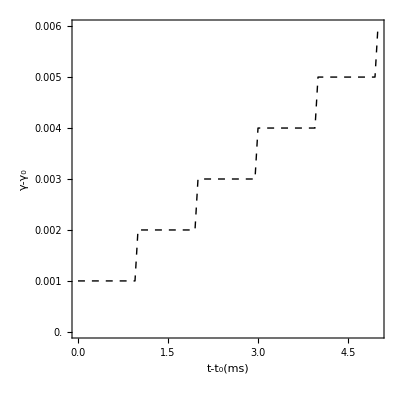
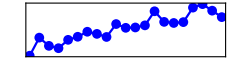
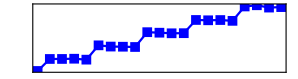
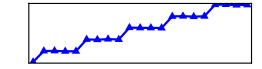

```mathematica
plt=Overlay[{
Overlay[{
Overlay[{strplt,
Show[p1,ImageSize->s1]},Alignment->{x1,y1}],
Show[p2,ImageSize->s2]},Alignment->{x2,y2}],
Show[p3,ImageSize->s3]},Alignment->{x3,y3}]/.{
s1->235,s2->298,s3->262,
x1->0.165,x2->0.84,x3->0.365,
y1->-0.49,y2->0.155,y3->0.7}
```

```mathematica
Export[figdir<>"/5B.png",plt];
```

```mathematica
Export[figdir<>"/5B.svg",plt];
```

```mathematica
Export[figdir<>"/5Bleft.eps",strplt];
Export[figdir<>"/5Bbot.eps",p1];
Export[figdir<>"/5Bmid.eps",p2];
Export[figdir<>"/5Btop.eps",p3];
```

### C

```mathematica
kls={0.1,0.2,0.5,1,2,5,10,20,50,100,200,500,1000};
dirs=fig5dir<>"/kcl"<>ToString[NumberForm[#,{2,1}]]&/@kls;
dt=10^(-6);
tfs=0.5;
engs=Transpose/@Table[Import[dr<>"/data/pe.txt","TSV"],{dr,dirs}];
te=Total/@engs;
ts=Range[0,0.49999,0.5/10000];
γs=Range[1,500]0.001;
eqengs=Table[Mean/@Partition[te[[i]],20],{i,Length[te]}];
dats=({γs[[1;;Length[#]]],#/75^2}ᵀ)&/@eqengs;
```

```mathematica
leg=logbarleg[1,1000,3,"BlueGreenYellow",ExponentFunction->1,{LegendLabel->Placed["k_xl\t",Bottom],LegendMarkerSize->{250,20},LabelStyle->Directive[Black,FontSize->28],TicksStyle->Black,LegendLayout->"Row"}]
```

```mathematica
idxs={4,5,6,7,10,13};
plt=
Show[
ListLogLogPlot[dats[[idxs,200;;]],
PlotStyle->"BlueGreenYellow",
Frame->True,
FrameStyle->Black,
FrameLabel->{"γ","w (pN/μm)"},
PlotMarkers->None
(*,FrameTicks->{{LogTicks[10,-3,3],LogTicks[10,-3,3,ShowTickLabels->False]},{Automatic,Automatic}},*)
],Plot[{2x-1.7,7/2x+2.5},{x,-4,10},PlotStyle->{{Darker[Blue],Dashed,Thick},{Darker[Green],Dashed,Thick}}],
BaseStyle->{FontFamily->"Arial",FontSize->22},
AspectRatio->0.8
];
```

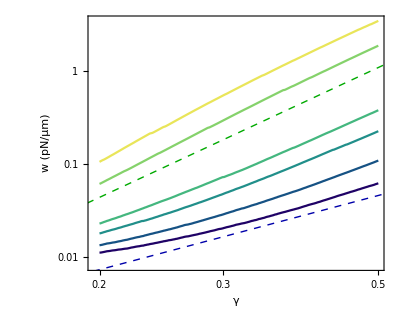

```mathematica
plt
```

```mathematica
Export[figdir<>"/5C.eps",plt];
```

```mathematica
Export[figdir<>"/5Cleg.png",leg];
```

### D (continued from C)

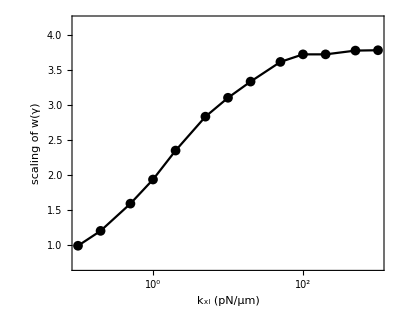

```mathematica
fs=Fit[#,{1,x},x]&/@Log[dats[[1;;,200;;]]];
exps=D[fs,x];
expdatsp={Log10[kls],exps}ᵀ;
plt=ListPlot[expdatsp,
PlotStyle->Black,
PlotRange->{0.7,4.2},
Joined->True,
PlotMarkers->{●,10},BaseStyle->FontSize->22,FrameLabel->{"k_xl (pN/μm)","scaling of w(γ)"},
FrameTicks->{{Automatic,Automatic},{LogTicks[10,-2,4],LogTicks[10,-2,4,ShowTickLabels->False]}},
AspectRatio->0.8,Axes->None]
```

```mathematica
Export[figdir<>"/5D.eps",plt];
```

### S5 (Continued from C)

```mathematica
stprop=engs[[All,1,2;;]]/te[[All,2;;]];
bendprop=engs[[All,2,2;;]]/te[[All,2;;]];
xlprop=engs[[All,4,2;;]]/te[[All,2;;]];
```

```mathematica
plt1=ListPlot[stprop[[All,1;;-1;;100]],PlotStyle->"BlueGreenYellow",PlotRange->{Automatic,{0,1}},
FrameLabel->{"strain","w_actin_stretch / w"},DataRange->{0,0.5},Joined->True,PlotMarkers->None];
plt2=ListPlot[bendprop[[All,1;;-1;;100]],PlotStyle->"BlueGreenYellow",PlotRange->{Automatic,{0,1}},
FrameLabel->{"strain","w_actin_bend / w"},DataRange->{0,0.5},Joined->True,PlotMarkers->None];
plt3=ListPlot[xlprop[[All,1;;-1;;100]],PlotStyle->"BlueGreenYellow",PlotRange->{Automatic,{0,1}},
FrameLabel->{"strain","w_xl / w"},DataRange->{0,0.5},Joined->True,PlotMarkers->None];
```

```mathematica
GraphicsRow[{plt1,plt2,plt3},ImageSize->1000]
```

```mathematica
Export[figdir<>"/S5D.pdf",plt3];
Export[figdir<>"/S5E.pdf",plt1];
Export[figdir<>"/S5F.pdf",plt2];
```

```mathematica
rngy={5*^-4,3.6};
engdens=engs/75^2;
p1 = ListLogPlot[engdens[[All,1,2;;-1;;100]],PlotStyle->"BlueGreenYellow",FrameLabel->{"strain","w_actin_stretch (pN/μm)"},DataRange->{0,0.5},PlotRange->{{0,0.5},rngy},Joined->True,PlotMarkers->None];
p2=ListLogPlot[engdens[[All,2,2;;-1;;100]],PlotStyle->"BlueGreenYellow",FrameLabel->{"strain","w_actin_bend (pN/μm)"},DataRange->{0,0.5},PlotRange->{{0,0.5},rngy},Joined->True,PlotMarkers->None];
p3=ListLogPlot[engdens[[All,4,2;;-1;;100]],PlotStyle->"BlueGreenYellow",FrameLabel->{"strain","w_xl (pN/μm)"},DataRange->{0,0.5},PlotRange->{{0,0.5},rngy},Joined->True,PlotMarkers->None];
```

```mathematica
GraphicsRow[{p3,p1,p2},ImageSize->1000]
```

```mathematica
Export[figdir<>"/S5A.pdf",p3];
Export[figdir<>"/S5B.pdf",p1];
Export[figdir<>"/S5C.pdf",p2];
```

```mathematica
Export[figdir<>"/shear_actin_bend.eps",p2];
```

### S3

```mathematica
nshears=Join[Flatten[Outer[Times,{1,10,100,1000},{2,5,10}]]];
dirs=Table[figS2dir<>"/nbw"<>ToString[n],{n,nshears}];
dt=10^(-7);
tfs=500*dt*nshears;
δt=dt*1000;
engs=Transpose/@Table[Import[dr<>"/data/pe.txt","TSV"],{dr,dirs}];
te=Total/@engs;
ts=Table[Range[0,tf,Max[dt,tf/10000]],{tf,tfs}];
ts[[5]]=Range[0,tfs[[5]],tfs[[5]]/12500];
ls=Floor[Length/@ts,100];
eng1dat=Table[{ts[[i,;;ls[[i]]]],te[[i,;;ls[[i]]]]}ᵀ,{i,1,Length[ls]}];
dts=eng1dat[[All,2,1]]-eng1dat[[All,1,1]];
dshears=0.5/Length/@eng1dat;
eng2dat=Table[{ts[[i,;;ls[[i]]]]*dshears[[i]]/dts[[i]],te[[i,;;ls[[i]]]]}ᵀ,{i,1,Length[ls]}];
logeng2dat=Table[{ts[[i,;;ls[[i]]]]*dshears[[i]]/dts[[i]],Log10[te[[i,;;ls[[i]]]]]}ᵀ,{i,1,Length[ls]}];
```

```mathematica
tixy=LogTicks[10,1,5];
etplt2=ListPlot[logeng2dat,
PlotStyle->"BlueGreenYellow",
PlotRange->{{0,0.5},{1.2,4.9}},
FrameLabel->{"Strain","Energy (pNμm)"},
FrameTicks->{{tixy,Automatic},{Automatic,Automatic}},
BaseStyle->FontSize->21,
PlotRange->{{0.001,0.5},Automatic},
PlotMarkers->None
]
```

```mathematica
Export[figdir<>"/S3.pdf",etplt2];
```

## Figure 6

```mathematica
kon0=1;
ρ0=4;
L0=15;
Lm=0.5;
koff0=1;
kend0=10;
rd0=kon0/(kon0+koff0);
fig6dir=outdir<>"/vf_r2/motility/koff1_kend10/sd1";
(*fig6dir=outdir<>"/vf_r2/testing/motility/kend100_koff0.1/";
fig6dir=outdir<>"/vf_r2/testing/motility/kend10_koff0.1_rc0.03/";*)
```

### A

```mathematica
dir=fig6dir<>"/kon_arr/kon";
ks={0.001,0.002,0.005,0.01,0.02,0.05,0.1,0.2,0.5,1,2};
idxs={1,6,9,11};
dirs=dir<>ToString[NumberForm[#,{1,3}]]&/@(ks[[idxs]]);
(*ks=Join[ks1,{3,4}];*)
konarr=pts[#,"actins"]&/@dirs;
maxf=401;
cf=ColorData[{"DeepSeaColors",{1,maxf}}];
cf2[i_]:=Blend[{Pink,Darker[Red]},(i-1)/(maxf-1)];
start=5;
fs=Table[
draw[
konarr[[j,{i+start}]],{},{},{},dirs[[-1]],False,25{{-1,1},{-1,1}},True,16,cf2[i]
],
{j,1,Length[konarr]},
{i,1,maxf,40}
];
pics=Show/@fs;
grow=GraphicsRow[pics,Spacings->20];
```

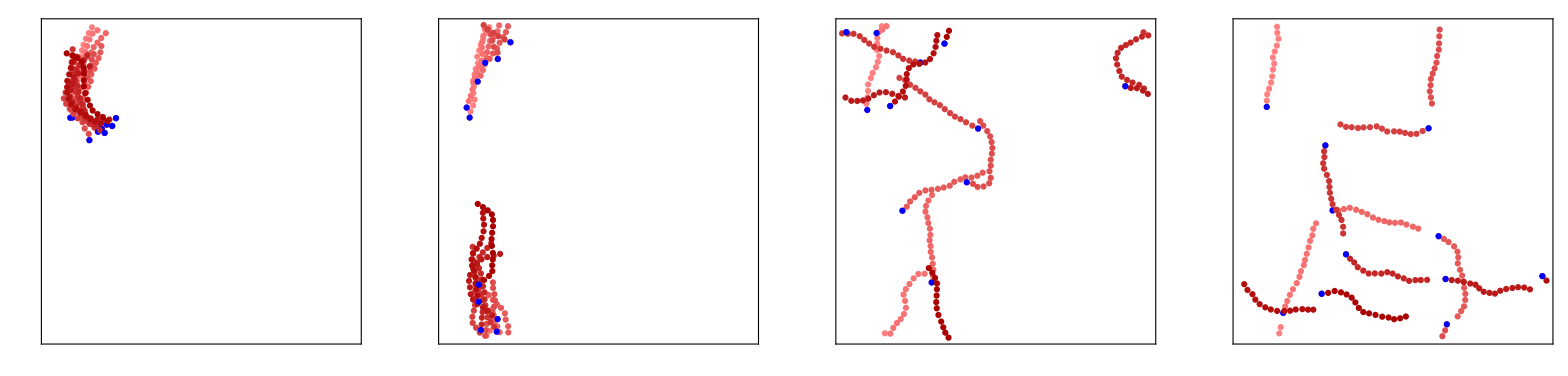

```mathematica
grow
```

```mathematica
Export[figdir<>"/6A_kon"<>StringRiffle[ToString/@ks[[idxs]],"_"]<>".pdf",grow];
```

### B

#### Green

```mathematica
dir1=fig6dir<>"/dens_arr/dens";
ρs1={0.01,0.02,0.05,0.1,0.2,0.5,1,2,5};
dir2=fig6dir<>"/dens_arr_dt2e-5/dens";
ρs2={3,4,6,7,9};
dirs1=dir1<>ToString[NumberForm[#,{1,2}]]&/@ρs1;
dirs2=dir2<>ToString[NumberForm[#,{1,2}]]&/@ρs2;
dirs=Join[dirs1[[1;;-2]],dirs2[[1;;2]],dirs1[[{-1}]],dirs2[[3;;]]];
ρs=Join[ρs1[[1;;-2]],ρs2[[1;;2]],ρs1[[{-1}]],ρs2[[3;;]]];

lks1=Table[pts[dr,"links"],{dr,dirs}];
drs=lks1[[All,2;;-1,All,1;;2]]-lks1[[All,1;;-2,All,1;;2]];
drps1=Map[rijP[#,{50,50}]&,drs,{3}];
vs1=Map[Norm[#]&,drps1,{3}];
norms=Map[Norm,lks1[[All,1;;-2,All,3;;4]],{3}];

rspar=lks1[[All,1;;-2,All,3;;4]]/norms;
rsperp=Table[{-rspar[[i,j,k,2]],rspar[[i,j,k,1]]},{i,Length[rspar]},{j,Length[rspar[[i]]]},{k,Length[rspar[[i,j]]]}];

vspar=Table[MapThread[Dot,{drps1[[i]],rspar[[i]]},2],{i,Length[drps1]}];
vsperp=Table[MapThread[Dot,{drps1[[i]],rsperp[[i]]},2],{i,Length[drps1]}];

dt=0.5;
muvs1=Mean/@Flatten/@vs1/dt;
par1=Mean/@Flatten/@vspar/dt;
perp1=Sqrt[-par1^2+muvs1^2];
```

#### Red Curve

```mathematica
dir2=fig6dir<>"/length_arr/nm";
nms=Range[2,26,2];
dirs=dir2<>ToString[#]&/@nms;

lks2=Table[pts[dr,"links"],{dr,dirs}];

drs=lks2[[All,2;;-1,All,1;;2]]-lks2[[All,1;;-2,All,1;;2]];
drps2=Map[rijP[#,{50,50}]&,drs,{3}];
vs2=Map[Norm[#]&,drps2,{3}];

norms=Map[Norm,lks2[[All,1;;-2,All,3;;4]],{3}];
vspar=Table[drps2[[i,t,j]].lks2[[i,t,j,3;;4]]/norms[[i,t,j]],{i,1,Length[drps2]},{t,1,Length[drps2[[i]]]},{j,1,Length[drps2[[i,t]]]}];
muvs2=Mean/@Flatten/@vs2/dt;

par2=Mean/@Flatten/@vspar/dt;
perp2=Sqrt[-par2^2+muvs2^2];
```

#### Blue Curve

```mathematica
dir1=fig6dir<>"/kon_arr/kon";
ks1={0.001,0.002,0.005,0.01,0.02,0.05,0.1,0.2,0.5,1,2};
dir2=fig6dir<>"/kon_arr_dt1e-5/kon3.000";
dir3=fig6dir<>"/kon_arr_dt2e-5/kon4.000";
dirs=Join[dir1<>ToString[NumberForm[#,{1,3}]]&/@ks1,{dir2,dir3}];
ks=Join[ks1,{3,4}];
lks3=Table[pts[dr,"links"],{dr,dirs}];

drs=lks3[[All,2;;-1,All,1;;2]]-lks3[[All,1;;-2,All,1;;2]];
drps3=Map[rijP[#,{50,50}]&,drs,{3}];
vs3=Map[Norm[#]&,drps3,{3}];

norms=Map[Norm,lks3[[All,1;;-2,All,3;;4]],{3}];

vspar=Table[MapThread[Dot,{drps3[[i]],lks3[[i,1;;-2,All,3;;4]]/norms[[i]]},2],{i,Length[drps3]}];
muvs3=Mean/@Flatten/@vs3/dt;
par3=Mean/@Flatten/@vspar/dt;

perp3=Sqrt[-par3^2+muvs3^2];
```

#### Whole Plot

```mathematica
a=1;
xvals1=ρs Lm L0 rd0^a;
xvals2=(ρ0 Lm(nms-1)) rd0^a;
xvals3=(ρ0 Lm L0)(ks/(ks+koff0))^a;
sz=10;
```

```mathematica
tab=
{{"","v_(||)","v_⊥"},
{"ρ_m",Graphics[{Green,Disk[]},ImageSize->sz],Graphics[{EdgeForm[Directive[Thick,Green]],White,Rectangle[]},ImageSize->sz]},
{"L",Graphics[{Red,Disk[{0,0},0.1]},ImageSize->sz],Graphics[{EdgeForm[Directive[Thick,Red]],White,Rectangle[]},ImageSize->sz]},
{"r_D",Graphics[{Blue,Disk[]},ImageSize->sz],Graphics[{EdgeForm[Directive[Thick,Blue]],White,Rectangle[]},ImageSize->sz]}};
leg=Grid[tab,BaseStyle->{FontSize->19,FontFamily->"Arial"},Frame->All,Spacings->{0.2,0.2},Background->{{LightGray,None},{LightGray,None}}];
vplt1=ListPlot[
{{xvals1,par1}ᵀ[[1;;-2]],{xvals2,par2}ᵀ,{xvals3,par3}ᵀ,
{xvals1,perp1}ᵀ[[1;;-2]],{xvals2,perp2}ᵀ,{xvals3,perp3}ᵀ},Joined->True,
PlotMarkers->{{●,10},{●,10},{●,10},{□,15},{□,15},{□,15}},
PlotStyle->{Green,Red,Blue,Green,Red,Blue},PlotRange->{{0,27},{0,1.1}},
FrameLabel->{"ρ_ml_mLr_D","v(μm/s)"}];
```

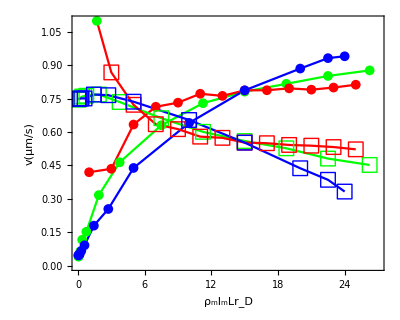

```mathematica
vplt1
```

```mathematica
vplt=Overlay[{vplt1,leg},Alignment->{0.1,-0.25}]
```

-Graphics- | v_(||) | v_⊥
ρ_m | -Graphics- | -Graphics-
L | -Graphics- | -Graphics-
r_D | -Graphics- | -Graphics-

```mathematica
Export[figdir<>"/6B.eps",vplt];
```

### C (Continued from B)

```mathematica
(*If Evaluating for the first time*)
ms1=Table[msdpc[drps1[[j,All,i]]],{j,1,Length[drps1]},{i,1,L0}];
Export[fig6dir<>"/dens_msds.dat",ms1];
ms2=Table[msdpc[drps2[[j,All,i]]],{j,1,Length[drps2]},{i,1,nms[[j]]-1}];
Export[fig6dir<>"/len_msds.dat",ms2];
ms3=Table[msdpc[drps3[[j,All,i]]],{j,1,Length[drps3]},{i,1,L0}];
Export[fig6dir<>"/kon_msds.dat",ms3];
```

LinkConnect::linkc: Unable to connect to LinkObject["/software/mathematica-10.2-x86_64/Executables/wolfram -subkernel -noinit -wstp", 2391, 17].

$Aborted

ParallelTable::nopar: No parallel kernels available; proceeding with sequential evaluation.

$Aborted

ParallelTable::nopar: No parallel kernels available; proceeding with sequential evaluation.

$Aborted

```mathematica
(*If already evaluated*)
ms1=ToExpression[Import[fig6dir<>"/dens_msds.dat","TSV"]];
ms2=ToExpression[Import[fig6dir<>"/len_msds.dat","TSV"]];
ms3=ToExpression[Import[fig6dir<>"/kon_msds.dat","TSV"]];
```

```mathematica
Dimensions/@ms3
```

{{15,2000},{15,2000},{15,2000},{15,2000},{15,2000},{15,2000},{15,2000},{15,2000},{15,2000},{15,2000},{15,956}}

```mathematica
(*Sort MSD data sets by their xval*)
msddats1=Table[{xvals1[[i]],{Range[2000]*dt,Mean[ms1[[i]]]}ᵀ},{i,1,Length[ms1]}];
msddats2=Table[{xvals2[[i]],{Range[2000]*dt,Mean[ms2[[i]]]}ᵀ},{i,1,Length[ms2]}];
msddats3=Table[{xvals3[[i]],{Range[Length[ms3[[i,1]]]]*dt,Mean[ms3[[i]]]}ᵀ},{i,1,Length[ms3]}];
allmsddats=Sort[Join[msddats1,msddats2,msddats3]];
allxvals=allmsddats[[All,1]];
```

```mathematica
Length[allxvals]
```

33

```mathematica
xidxs=Range[1,33];
tidxs=Union[Round[10^Range[0,Log10[200],0.15]]];
logxvals=Log[allxvals[[xidxs]]];
cf=ColorData[{"BlueGreenYellow",{Min[logxvals],Max[logxvals]}}];
msdplt=Show[ListLogLogPlot[allmsddats[[xidxs,2,tidxs]],
PlotRange->Full,
PlotStyle->cf/@logxvals,
FrameLabel->{"δt (s)",Style["⟨|r(t+δt)-r(t)|^2⟩ (μm^2)",FontSize->20]},
PlotMarkers->ConstantArray[{●,15},6],
Joined->False
],
Plot[{x-2,2x},{x,-1,200},PlotStyle->{{Blue,Thick,Dashing[Large]},{Orange,Thick,Dashing[Large]}}]
]
```

```mathematica
Export[figdir<>"/6C_0.03-25.eps",msdplt];
```

```mathematica
x=logbarleg[0.03,25,4,"BlueGreenYellow",{4,1},{LegendLabel->Placed["ρ_ml_mLr_D",Bottom],LegendMarkerSize->{40,250},LabelStyle->Directive[Black,FontSize->30],TicksStyle->Black}]
```

```mathematica
Export[figdir<>"/6C_leg.pdf",x];
```

### D

```mathematica
fig6Ddir=vfdir<>"/motility/koff1_kend10/";
```

#### simulation

```mathematica
mdenss={0.01,0.02,0.05,0.1,0.2,0.5,1,2,5(*,10*)};
ddirs=Flatten[Table[fig6Ddir<>"sd"<>ToString[i]<>"/dens_arr/dens"<>ToString[NumberForm[md,{2,2}]],{i,5},{md,mdenss}]];

nms=Range[2,26,2];
ldirs=Flatten[Table[fig6Ddir<>"sd"<>ToString[i]<>"/length_arr/nm"<>ToString[nm],{i,5},{nm,nms}]];

ks={0.001,0.002,0.005,0.01,0.02,0.05,0.1,0.2,0.5,1,2};
kdirs=Flatten[Table[fig6Ddir<>"sd"<>ToString[i]<>"/kon_arr/kon"<>ToString[NumberForm[k,{2,3}]],{i,5},{k,ks}]];

dirs=Join[ddirs,ldirs,kdirs];
maxX=50;
```

```mathematica
actext=Table[pts3[dir,"actins_ext"],{dir,dirs}];
cms=Map[Mean,actext[[All,All,All,1;;2]],{2}];
cms=MovingAverage[#,20]&/@cms;
lkext=cms[[All,2;;]]-cms[[All,;;-2]];
```

```mathematica
lps=Table[plThsq[lkext[[i]],maxX],{i,Length[lkext]}];
```

```mathematica
xvals1=mdenss Lm L0 rd0;
xvals2=(ρ0 Lm(nms-1)) rd0;
xvals3=(ρ0 Lm L0)(ks/(ks+(0.9koff0+0.1kend0)));

bnd1=(5Length[mdenss]);
bnd2=bnd1+5Length[nms];
lps1=Mean[Partition[lps[[1;;bnd1]],Length[mdenss]]];
lps2=Mean[Partition[lps[[(bnd1+1);;bnd2]],Length[nms]]];
lps3=Mean[Partition[lps[[(bnd2+1);;]],Length[ks]]];
```

```mathematica
lperrs1=StandardDeviation[Partition[lps[[1;;bnd1]],Length[mdenss]]]/Sqrt[5];
lperrs2=StandardDeviation[Partition[lps[[(bnd1+1);;bnd2]],Length[nms]]]/Sqrt[5];
lperrs3=StandardDeviation[Partition[lps[[(bnd2+1);;]],Length[ks]]]/Sqrt[5];
```

#### theory: duke holy 1995

```mathematica
f=1;
ll[x_,y_]:=x f<y;
gg[x_,y_]:=x/f>y;
```

```mathematica
Lp=17;
kbT=0.004;
visc=0.001;
maxBindDist=0.063;
ka=1;
v0=1;
γ=kbT/visc;
Ls=Range[2,25];
σ0=ρ0;
σx=maxBindDist^(-5/3)Lp^(-1/3);
σxx=(γ/v0 )^(-5/6)Lp^(-1/3);
davg0=σ0 Lp^(1/5);

ClearAll[davg,savg,pcur,dth,persist];
davg[σ_,σp_:σx, σpp_:σxx]:=
If[ll[σ,σpp],1/(σ Sqrt[γ/v0]),
If[gg[σ,σpp]&&ll[σ,σp],σ^(-2./5)Lp^(1/5),
If[gg[σ,σp],1/(σ maxBindDist)],-1]
];
savg[l_,d_]:=If[d≥0,(l+2d)/(l+3d)(d^2/l)(Exp[l/d]-1-l/d),-1];
pcur[σ_,σpp_:σxx]:=If[σ>σpp,Lp,Lp (σ/σpp)^2];
dth[ρ_,L_]:=3/(ρ L^2);
persist[ρ_,L_,σp_:σx,σpp_:σxx]:=With[{s=savg[L,davg[ρ,σp,σpp]]},If[s>0,1/(1/pcur[ρ,σpp]+dth[ρ,L]^2/s),-1]];

pr={{-1.5,1.5},{-1,1.5}};
prplt1=ListPlot[Table[Log10[{ρ0 Lm L rd0,persist[ρ0,L]}],{L,0.01,26,0.01}],PlotStyle->{Red,Thick,Dashed},PlotRange->pr,Joined->True,PlotMarkers->None];
prplt2=ListPlot[Table[Log10[{ρ0 Lm L0 rD,persist[ρ0*rD,L0,σx,σxx ]}],{rD,.001/1.01,3/4,0.01}],PlotStyle->{Blue,Thick,Dashed},PlotRange->pr,Joined->True,PlotMarkers->None];
prplt3=ListPlot[  
Table[Log10[{ρ Lm L0 rd0,persist[ρ,L0]}],{ρ,0.001,6,0.01}],PlotStyle->{Green,Thick,Dashed},PlotRange->pr,Joined->True,PlotMarkers->None];
```

#### plot theory + simulation

```mathematica
xtix=ytix=LogTicks[10,-3,3];
dplt=ListPlot[
Log10[{{xvals1,lps1}ᵀ,{xvals2,lps2}ᵀ,({xvals3,lps3}ᵀ)[[1;;-3]]
}],
Joined->Join[ConstantArray[True,3],ConstantArray[True,6]],
PlotMarkers->Join[ConstantArray[{●,15},3],ConstantArray["·",6]],
PlotStyle->{Green,Red,Blue},
FrameLabel->{"ρ_ml_mLr_D","Path Persistence\nLength (μm)"},
Filling->{4->{5},6->{7},8->{9}},
FrameTicks->{{ytix,Automatic},{xtix,Automatic}},
FillingStyle->Directive[Opacity[0.25],Thickness[0.01]],
PlotRange->pr,
Axes->None];
```

```mathematica
scplt=Show[{dplt,prplt1,prplt2,prplt3}]
```

```mathematica
Export[figdir<>"/6D_gg10.pdf",scplt]
```

/project/weare-dinner/simonfreedman/cytomod/out/vf_r2/figs/6D_gg10.pdf

## Figure 7, S7

### 7

```mathematica
seeds=Range[20];
dirs=fig7dir<>"/seed"<>ToString[#]<>"e7"&/@seeds;
dir=dirs[[15]];
```

#### A

```mathematica
acts=pts[dir,"actins"];
links=pts[dir,"links"][[1;;-2]];
ams=pts[dir,"amotors"][[1;;-2]];
pms=pts[dir,"pmotors"][[1;;-2]];
```

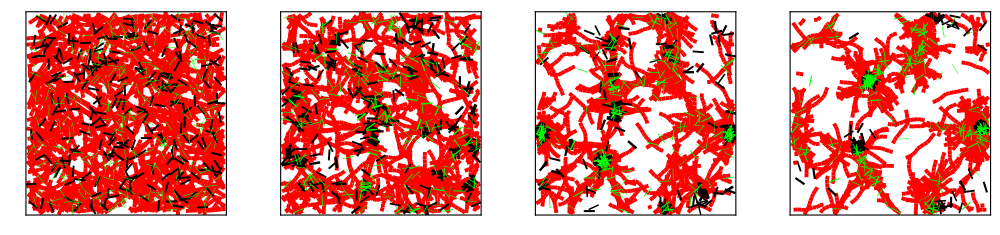

```mathematica
idxs={1,51,151,399};
frs=draw[{},links[[idxs]],ams[[idxs,1;;-1;;2]],pms[[idxs,1;;-1;;10]],dir,False,{50,50},1,False,16];
GraphicsRow[frs,ImageSize->1000]
```

```mathematica
Export[figdir<>"/7A_t0_50_150_398.eps",GraphicsRow[frs,ImageSize->1000]];
```

#### B

```mathematica
nm=11;
nparts=500*nm;
rngs=Table[Join[Range[1,nm i],Range[nm(i+1)+1,nparts]],{i,0,nparts/nm-1}];
(*All pairs of actin beads that are not on the same filament*)
allPairs=Union[Sort/@Flatten[
Table[{i,j},
{i,nparts},
{j,RandomSample[rngs[[Quotient[i-1,nm]+1]],1000]}],1]];
(*A sample of them*)
idxs={1,51,101,201,399};
sampPairs=RandomSample[allPairs,500*499/2];
gr=rdftraj[acts[[idxs]],{50,50},0.1,5,sampPairs];
```

```mathematica
cf=ColorData[{"BlueGreenYellow",{Min[idxs],Max[idxs]}}];
ts=idxs-1;
```

```mathematica
grplot=ListPlot[gr,(*PlotStyle->Table[{cf[t],Thick},{t,ts}],*)FrameLabel->{"distance (μm)","radial distr. func."},Joined->True,PlotRange->Full,PlotLegends->Placed[SwatchLegend[ts,LegendLabel->"time (s)",LegendMarkerSize->20,Spacings->0,LegendLayout->"ReversedColumn"],{0.8,0.65}],DataRange->{0.025,4.975}]
```

```mathematica
Export[figdir<>"/7B.eps",grplot];
```

#### C

C and D, and S4 require you to have run the Python divergence calculating code "div_by_vbin.py" available in the versatile_framework _paper directory; see versatile_framework_paper/README.md for details

```mathematica
t=245;
t=51;
sd=15;
ClearAll[wft,uft,vft,divft];
wft=Import[dirs[[sd]]<>"/analysis/vfield_weights_nbins10_dt10_thresh10/t"<>ToString[t-5]<>".txt","TABLE"];
uft[i_,j_]:=velx[i,j,wft];
vft[i_,j_]:=vely[i,j,wft];
divft[i_,j_]:=div[i,j,wft];
dplt=DensityPlot[divft[x,y],{x,-25,25},{y,-25,25},PlotRange->{25{-1,1},25{-1,1},All},
ColorFunction->ColorData[{"ThermometerColors",0.07{1,-1}}],ColorFunctionScaling->False(*,PlotLegends->Automatic*)];
vplt=VectorPlot[{uft[x,y],vft[x,y]},{x,-25,25},{y,-25,25},PlotRange->25{{-1,1},{-1,1}}(*,Background->None*)];
```

```mathematica
Export[figdir<>"/7C_lowk_t50.png",Overlay[{dplt,vplt}]];
```

#### D

```mathematica
(*calculate strain for the first time*)
(*acts=Table[pts[dr,"actins"],{dr,dirs}];
strs=Map[filstrain,acts];
Export[fig7dir<>"/strains_all.dat",strs];*)
```

```mathematica
(*densdivs=Table[Import[dir<>"/analysis/dens_div_dr1_nbins10.dat","TSV"],{dir,dirs}];*)
strs=importCheck[fig7dir<>"/strains_all.dat"];
```

```mathematica
dt=10;
```

```mathematica
bcs=Table[ToExpression[Import[dr<>"/analysis/bin_counts_dr1.dat","TSV"]],{dr,dirs}];
bcsdt=MovingAverage[#,dt]&/@bcs;
bcsdt=0.5(bcsdt[[All,2;;]]+bcsdt[[All,;;-2]]);
```

```mathematica
divs=Table[ToExpression@Import[dir<>"/analysis/div_dr1_nbins10_dt"<>ToString[dt]<>".dat","TSV"],{dir,dirs}];
densdivsdr1=Table[Total[bcsdt[[i,t]]divs[[i,t]],2],{i,Length[bcsdt]},{t,Length[bcsdt[[i]]]}];
(*densdivs=Table[Import[dir<>"/analysis/dens_div_dr1_nbins10.dat","TSV"],{dir,dirs}];*)
meandivdr1=Mean[densdivsdr1];
errdivdr1=StandardDeviation[densdivsdr1]/Sqrt[Length[seeds]];
```

```mathematica
tf=399;
strmus=Map[Mean,strs[[All,;;tf]],{2}];
meanstr=Mean[strmus];
errstr=StandardDeviation[strmus]/Sqrt[Length[seeds]];
```

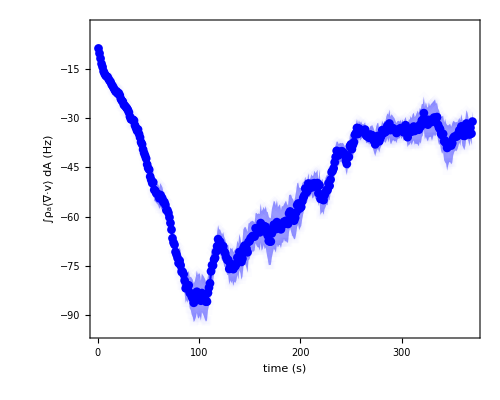
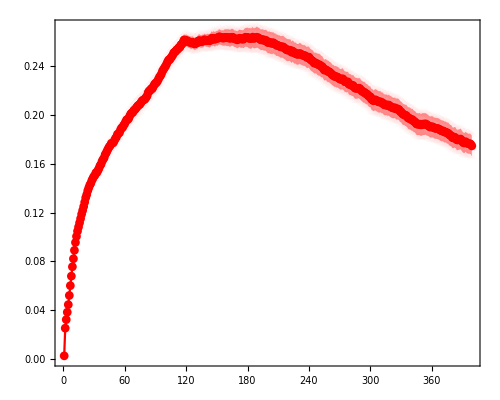

```mathematica
lp1=ListPlot[{meandivdr1,meandivdr1-errdivdr1,meandivdr1+errdivdr1},
Joined->True,
PlotStyle->{Blue,{Blue,Opacity[0.01]},{Blue,Opacity[0.01]}},
Filling->{2->{3}},
FillingStyle->Opacity[0.4],
PlotRange->{-95,-2},
FrameStyle->{{Blue,Black},{Black,Black}},
FrameTicks->{{Automatic,Automatic},{LinTicks[0,400,100,10],Automatic}},
FrameLabel->{"time (s)","∫ρ_a⟨∇·v⟩ dA  (Hz)"},
ImagePadding->100,
ImageSize->500];

lp2=ListPlot[{meanstr,meanstr-errstr,meanstr+errstr},
Joined->True,PlotRange->Full,
PlotStyle->{Red,{Red,Opacity[0.01]},{Red,Opacity[0.01]}},
Filling->{2->{3}},
FillingStyle->Opacity[0.4],
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
FrameStyle->{{Red,Red},{Black,Black}},
FrameLabel->{"","filament strain","",""},
ImagePadding->100,
ImageSize->500];
divstrplt=Overlay[
{Show[lp1,Frame->{{True,False},{True,True}}],
Show[lp2,Frame->{{False,True},{False,False}},
FrameTicks->All,
FrameLabel->{"","","",Rotate["filament strain",Pi]}]}]
```

```mathematica
Export[figdir<>"/7D_lowk.png",divstrplt];
```

### S7

```mathematica
seeds=Range[20];
dirs=figS3dir<>"/seed"<>ToString[#]<>"e7"&/@seeds;
dir=dirs[[15]];
```

#### A

```mathematica
acts=pts[dir,"actins"];
links=pts[dir,"links"][[1;;-2]];
ams=pts[dir,"amotors"][[1;;-2]];
pms=pts[dir,"pmotors"][[1;;-2]];
```

```mathematica
idxs={1,101,251,399};
frs=draw[{},links[[idxs]],ams[[idxs,1;;-1;;2]],pms[[idxs,1;;-1;;10]],dir,False,{50,50},1,False,16];
GraphicsRow[frs,ImageSize->1000]
```

-Graphics-

```mathematica
Export[figdir<>"/7A_t0_50_150_398_lowk.eps",GraphicsRow[frs,ImageSize->1000]];
```

#### B

```mathematica
nm=11;
nparts=500*nm;
rngs=Table[Join[Range[1,nm i],Range[nm(i+1)+1,nparts]],{i,0,nparts/nm-1}];
(*All pairs of actin beads that are not on the same filament*)
allPairs=Union[Sort/@Flatten[
Table[{i,j},
{i,nparts},
{j,RandomSample[rngs[[Quotient[i-1,nm]+1]],1000]}],1]];
(*A sample of them*)
idxs={1,101,201,301,399};
sampPairs=RandomSample[allPairs,500*499/2];
gr=rdftraj[acts[[idxs]],{50,50},0.1,5,sampPairs];
```

```mathematica
cf=ColorData[{"BlueGreenYellow",{Min[idxs],Max[idxs]}}];
ts=idxs-1;
```

```mathematica
grplot=ListPlot[gr,(*PlotStyle->Table[{cf[t],Thick},{t,ts}],*)FrameLabel->{"distance (μm)","radial distr. func."},Joined->True,PlotRange->Full,PlotLegends->Placed[SwatchLegend[ts,LegendLabel->"time (s)",LegendMarkerSize->20,Spacings->0,LegendLayout->"ReversedColumn"],{0.8,0.65}],DataRange->{0.025,4.975}]
```

```mathematica
Export[figdir<>"/7B.eps",grplot];
```

```mathematica
Export[figdir<>"/7B_lowk.eps",grplot];
```

#### C

C and D, and S4 require you to have run the Python divergence calculating code “div_by_vbin.py” available in the versatile_framework _paper directory; see versatile_framework_paper/README.md for details

```mathematica
t=245;
t=51;
sd=15;
ClearAll[wft,uft,vft,divft];
wft=Import[dirs[[sd]]<>"/analysis/vfield_weights_nbins10_dt10_thresh10/t"<>ToString[t-5]<>".txt","TABLE"];
uft[i_,j_]:=velx[i,j,wft];
vft[i_,j_]:=vely[i,j,wft];
divft[i_,j_]:=div[i,j,wft];
dplt=DensityPlot[divft[x,y],{x,-25,25},{y,-25,25},PlotRange->{25{-1,1},25{-1,1},All},
ColorFunction->ColorData[{"ThermometerColors",0.07{1,-1}}],ColorFunctionScaling->False(*,PlotLegends->Automatic*)];
vplt=VectorPlot[{uft[x,y],vft[x,y]},{x,-25,25},{y,-25,25},PlotRange->25{{-1,1},{-1,1}}(*,Background->None*)];
```

```mathematica
Export[figdir<>"/7C_lowk_t50.png",Overlay[{dplt,vplt}]];
```

#### D

```mathematica
(*to calculate strains for the first time*)
(*
acts=Table[pts[dr,"actins"],{dr,dirs}];
strs=Map[filstrain,acts];
Export[figS3dir<>"/strains_all.dat",strs];*)
```

```mathematica
strs=importCheck[figS3dir<>"/strains_all.dat"];
```

```mathematica
bcs=Table[ToExpression[Import[dr<>"/analysis/bin_counts_dr1.dat","TSV"]],{dr,dirs}];
bcsdt=MovingAverage[#,dt]&/@bcs;
bcsdt=0.5(bcsdt[[All,2;;]]+bcsdt[[All,;;-2]]);
```

```mathematica
divs=Table[ToExpression@Import[dir<>"/analysis/div_dr1_nbins10_dt"<>ToString[dt]<>".dat","TSV"],{dir,dirs}];
```

```mathematica
densdivsdr1=Table[Total[bcsdt[[i,t]]divs[[i,t]],2],{i,Length[bcsdt]},{t,Length[bcsdt[[i]]]}];
```

```mathematica
(*densdivs=Table[Import[dir<>"/analysis/dens_div_dr1_nbins10.dat","TSV"],{dir,dirs}];*)
meandivdr1=Mean[densdivsdr1];
errdivdr1=StandardDeviation[densdivsdr1]/Sqrt[Length[seeds]];
```

```mathematica
tf=379;
strmus=Map[Mean,1-strs[[All,;;tf]]/10,{2}];
meanstr=Mean[strmus];
errstr=StandardDeviation[strmus]/Sqrt[Length[seeds]];
```

```mathematica
divrng={-110,8};
```

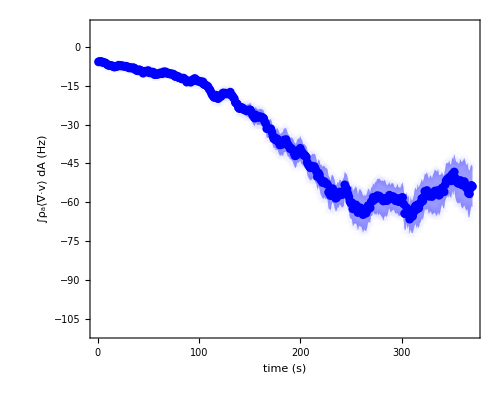
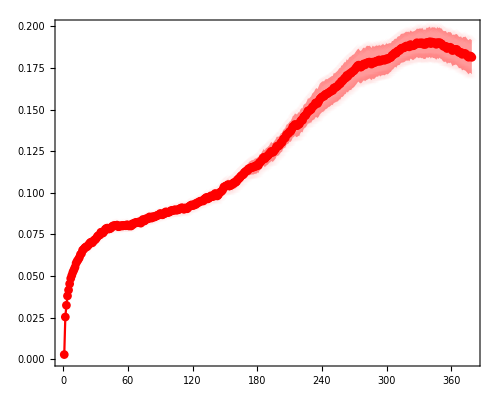

```mathematica
lp1=ListPlot[{meandivdr1,meandivdr1-errdivdr1,meandivdr1+errdivdr1},
Joined->True,
PlotStyle->{Blue,{Blue,Opacity[0.01]},{Blue,Opacity[0.01]}},
Filling->{2->{3}},
FillingStyle->Opacity[0.4],
PlotRange->divrng,
FrameStyle->{{Blue,Black},{Black,Black}},
FrameTicks->{{Automatic,Automatic},{LinTicks[0,400,100,10],Automatic}},
FrameLabel->{"time (s)","∫ρ_a⟨∇·v⟩ dA  (Hz)"},
ImagePadding->100,
ImageSize->500];

lp2=ListPlot[{meanstr,meanstr-errstr,meanstr+errstr},
Joined->True,PlotRange->Full,
PlotStyle->{Red,{Red,Opacity[0.01]},{Red,Opacity[0.01]}},
Filling->{2->{3}},
FillingStyle->Opacity[0.4],
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
FrameStyle->{{Red,Red},{Black,Black}},
FrameLabel->{"","filament strain","",""},
ImagePadding->100,
ImageSize->500];
divstrplt=Overlay[
{Show[lp1,Frame->{{True,False},{True,True}}],
Show[lp2,Frame->{{False,True},{False,False}},
FrameTicks->All,
FrameLabel->{"","","",Rotate["filament strain",Pi]}]}]
```

```mathematica
Export[figdir<>"/S7D.png",divstrplt];
```

#### E (Weighted by density)

```mathematica
dr=1;
dt=10;
fov=50;
t=251;
sd=15;
(*divt=Table[divft[x,y],{x,-24.5,24.5,1},{y,-24.5,24.5,1}];*)
divt=Import[dirs[[sd]]<>"/analysis/div_dr"<>ToString[dr]<>"_nbins10_dt"<>ToString[dt]<>".dat","Table"][[t-5]];
divt=Partition[Map[ToExpression[StringReplace[#,{","->"","{"->"","}"->""}]]&,divt],50];
bct=ToExpression[Import[dirs[[sd]]<>"/analysis/bin_counts_dr"<>ToString[dr]<>".dat","TSV"]][[t-5]];
xs=ys=Range[-fov/2+0.5,fov/2-0.5,1];
dat=Flatten[Table[{xs[[i]],ys[[j]],divt[[i,j]]*bct[[i,j]]},{i,Length[xs]},{j,Length[ys]}],1];
```

```mathematica
dplt2=ListDensityPlot[dat,PlotRange->{25{-1,1},25{-1,1},All},
ColorFunction->ColorData[{"ThermometerColors",0.15{1,-1}}],ColorFunctionScaling->False,FrameTicksStyle->White,InterpolationOrder->0];
```

```mathematica
Overlay[{dplt2,vplt}]
```

```mathematica
Export[figdir<>"/S7E.png",Overlay[{dplt2,vplt}]];
```

#### F

```mathematica
fov=50;tf=379;dt=10;
drs={1,2,5,10,25,50};
```

```mathematica
bcsdr=Table[Map[Total[Flatten[#]]&,Partition[bcsdt[[i,t]],{dr,dr}],{2}],{dr,drs},{i,Length[bcsdt]},{t,Length[bcsdt[[i]]]}];
divsdr=Table[Map[Total[Flatten[#]]&,Partition[divs[[i,t]],{dr,dr}],{2}],{dr,drs},{i,Length[divs]},{t,Length[divs[[i]]]}];
rhodivs=Table[Total[bcsdr[[i,j,t]]*divsdr[[i,j,t]]/drs[[i]]^2,2],{i,Length[divsdr]},{j,Length[divsdr[[i]]]},{t,Length[divsdr[[i,j]]]}];
meandiv=Mean/@rhodivs;
```

```mathematica
meandivdrs=meandiv;
```

```mathematica
divrng={-70,2};
```

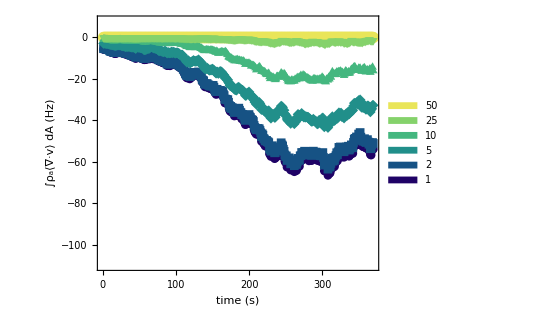

```mathematica
divdrplt=ListPlot[meandivdrs,
PlotStyle->"BlueGreenYellow",
Joined->True,
PlotRange->divrng,
FrameLabel->{"time (s)","∫ρ_a⟨∇·v⟩ dA  (Hz)"},
PlotLegends->Placed[SwatchLegend[drs,Spacings->0,LegendLayout->"ReversedColumn",LegendMarkerSize->15,LabelStyle->FontSize->17,LegendLabel->Placed[Rotate["(dA)^(1/2)(μm)",Pi/2],Left]],{0.16,0.33}],
FrameTicks->{{Automatic,Automatic},{LinTicks[0,400,100,10],Automatic}}]
```

```mathematica
Export[figdir<>"/S7F.eps",divdrplt];
```

#### G

```mathematica
dts={1,2,5,10,20};
fov=50;tf=380;
```

```mathematica
bcs=Table[ToExpression[Import[dr<>"/analysis/bin_counts_dr1.dat","TSV"]],{dr,dirs}];
```

```mathematica
Dimensions[bcs]
```

{20,380,50,50}

```mathematica
(*dr=1;*)
(*bcsdr=Table[Map[Total[Flatten[#]]&,Partition[bcs[[i,t]],{dr,dr}],{2}],{i,Length[bcs]},{t,Length[bcs[[i]]]}];*)
bcsdts=Table[MovingAverage[bcs[[i]],dt],{dt,dts},{i,Length[bcs]}];
bcsdts=0.5(bcsdts[[All,All,2;;]]+bcsdts[[All,All,;;-2]]);
```

```mathematica
divsdts=Table[ToExpression@Import[dir<>"/analysis/div_dr1_nbins10_dt"<>ToString[dt]<>".dat","TSV"],{dt,dts},{dir,dirs}];
```

```mathematica
rhodivsdts=Table[Total[bcsdts[[i,j,t]]*divsdts[[i,j,t]],2],{i,Length[divsdts]},{j,Length[divsdts[[i]]]},{t,Length[divsdts[[i,j]]]}];
```

```mathematica
meandivdts=Mean/@rhodivsdts;
```

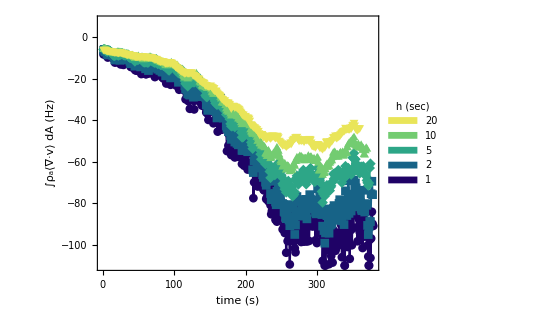

```mathematica
divdtplt=ListPlot[meandivdts,
PlotStyle->"BlueGreenYellow",
Joined->True,
PlotRange->divrng,
FrameLabel->{"time (s)","∫ρ_a⟨∇·v⟩ dA  (Hz)"},
PlotLegends->Placed[SwatchLegend[dts,Spacings->0,LegendLayout->"ReversedColumn",LegendMarkerSize->15,LabelStyle->FontSize->17,LegendLabel->Placed["  h (sec)",Bottom]],{0.2,0.35}(*{0.8,0.25}*)],
FrameTicks->{{Automatic,Automatic},{LinTicks[0,400,100,10],Automatic}}]
```

```mathematica
Export[figdir<>"/S7G.eps",divdtplt];
```

## S4

```mathematica
dx=1;
L=20;
nfils=20;
nlks=L/dx;
nacts=nlks+1;
teq=1000;
lppred=17;
xs=Range[dx,L-dx,dx];
maxl=5;
```

### A

```mathematica
figS4Adir=figS4dir<>"/fiber20/seg1.00";
acts=Partition[#,nacts]&/@ptsCS[figS4Adir,"objects"];
lks=acts[[All,All,2;;]]-acts[[All,All,;;-2]];

angs=Map[anglesTCS,lks,{2}];
angsbw=Map[anglesBwT,angs,{2}];

th2s=Map[th2,angsbw,{2}];
muths=Mean[th2s[[teq;;]]];
muthsmu=Mean[muths];
muthserr=StandardDeviation[muths]/Sqrt[nfils];

ccfs=Map[ccf,angsbw,{2}];
muccfs=Mean[ccfs[[teq;;-1]]];
muccfsmu=Mean[muccfs];
muccferr=StandardDeviation[muccfs]/Sqrt[nfils];
```

```mathematica
th2plt=Show[
ListPlot[{
{xs,muthsmu}ᵀ,
{xs,muthsmu-muthserr}ᵀ,
{xs,muthsmu+muthserr}ᵀ},
FrameLabel->{"","","",Rotate[Style["⟨θ^2(ℓ)⟩",Blue],Pi]},
FrameStyle->Blue,
Frame->{{False,True},{False,False}},
FrameTicks->{{None,All},{None,None}},
(*Comment out next three lines if you don't want joined*)
(**)
(*PlotStyle->{Blue,{Blue,Opacity[0.01]},{Blue,Opacity[0.01]}},
PlotMarkers->{{●,10},{○,0.01},{○,0.01},{●,5},{○,0.01},{○,0.01}},
Joined->{False,True,True},*)
(**)
(*Uncomment next four line if you don't want joined*)

FillingStyle->Directive[Opacity[1],Thickness[0.003]],
PlotMarkers->{{●,12},"+","+"},
PlotStyle->Blue,
Joined->False,

Filling->{2->{3}},
PlotRange->{{0,20},Automatic}
],
Plot[{x/(lp)},{x,0,50},PlotStyle->{Thick,Dashing[Large],Blue}]
];
```

```mathematica
ccfplt=Show[
ListLogPlot[{
{xs,muccfsmu}ᵀ,
{xs,muccfsmu-muccferr}ᵀ,
{xs,muccfsmu+muccferr}ᵀ},
FrameLabel->{"ℓ (μm)",Style["⟨cosθ(ℓ)⟩",Red]},
FrameStyle->{{Red,Automatic},{Black,Black}},
Frame->{{True,False},{True,True}},
FrameTicks->{{All,None},{All,Automatic}},
(*Comment out next three lines if you don't want joined*)
(**)
(*PlotStyle->{Red,{Red,Opacity[0.01]},{Red,Opacity[0.01]}},
PlotMarkers->{{●,10},{○,0.01},{○,0.01},{●,5},{○,0.01},{○,0.01}},
Joined->{False,True,True},*)
(**)
(*Uncomment next four line if you don't want joined*)
(**)
FillingStyle->Directive[Opacity[1],Thickness[0.003]],
PlotMarkers->{{●,12},"+","+"},
PlotStyle->Red,
Joined->False,
(**)
Filling->{2->{3}},
PlotRange->{{0,20},Automatic}],
LogPlot[{Exp[-x/(2lp)]},{x,0,50},PlotStyle->{Thick,Dashing[Large],Red}]
];
```

```mathematica
{ccfplt,th2plt}
```

{-Graphics-,-Graphics-}

```mathematica
Export[figdir<>"/S4A_red.eps",ccfplt];
Export[figdir<>"/S4A_blue.eps",th2plt];
```

### C

```mathematica
kbdir=figS4dir<>"/fiber20_seg1";
kbs={0.005,0.01,0.02,0.05,0.1,0.2,0.5,1.0,2.0,5,10,20,50,100,200,500};
kbdirs=kbdir<>"/kb"<>ToString[NumberForm[#,{1,3},ExponentFunction->(Null&)]]&/@kbs;
```

```mathematica
acts=Table[Partition[#,nacts]&/@ptsCS[dir,"objects"],{dir,kbdirs}];
lks=acts[[All,All,All,2;;]]-acts[[All,All,All,;;-2]];
lps=Table[plMeanThsq[lks[[i,All,j]],dx,L,maxl],{i,Length[lks]},{j,Length[lks[[i,1]]]}];
lpmeans=Mean/@lps;
```

```mathematica
lplpplt=Show[
ListLogLogPlot[
{{kbs/0.004,lpmeans}ᵀ(*,
{kbs[[3;;]]/0.004,1/msmidkb[[3;;]]}ᵀ*)
},
PlotMarkers->{●,15},
PlotStyle->{Red,{Blue,Opacity[0.75]}},
Joined->False
],
LogLogPlot[x,{x,0.1,500000},PlotStyle->{Black,Dashing[0.02](*,Thick*)}],
FrameLabel->{"κ_B (k_BT×μm)","L_p(μm)"}];
```

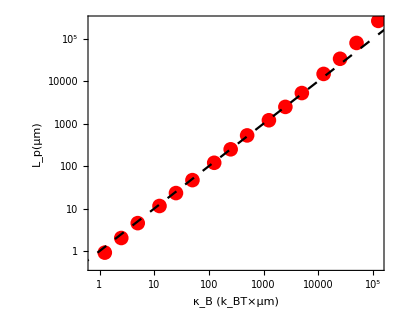

```mathematica
lplpplt
```

```mathematica
Export[figdir<>"/S4B.eps",lplpplt];
```

### B

#### Red

```mathematica
dxdir=csoutdir<>"/vf_r2/pl/fiber20_dt1e-5/";
dxs={0.08,0.1,0.2,0.25,0.4,0.5,0.8,1,2,2.5,4};
dxdirs=dxdir<>"/seg"<>ToString[NumberForm[#,{2,2},ExponentFunction->(Null&)]]&/@dxs;
nacts=L/dxs+1;
acts=ptsCS[#,"objects"]&/@dxdirs;
actsp=Table[Partition[#,Round[nacts[[i]]]]&/@acts[[i]],{i,Length[nacts]}];
lks=actsp[[All,All,All,2;;]]-actsp[[All,All,All,;;-2]];
lps=Table[plMeanThsq[lks[[i,All,j]],dxs[[i]],L,maxl],{i,Length[lks]},{j,Length[lks[[i,1]]]}];
lpmeans=Mean/@lps;
lperrs=(StandardDeviation/@lps)/Sqrt[nfils];
```

```mathematica
lpmmeanscs=lpmeans;
lperrscs=lperrs;
```

```mathematica
lpmeanscs=lpmmeanscs[[1;;-2]];
lperrscs=lperrscs[[1;;-2]];
```

```mathematica
Export[csoutdir<>"/vf_r2/pl/fiber20_dt1e-5/pls_mu_err.dat",{lpmmeanscs,lperrscs}];
```

```mathematica
ldat=importCheck[csoutdir<>"/vf_r2/pl/fiber20_dt1e-5/pls_mu_err.dat"];
```

```mathematica
{lpmeanscs,lperrscs}=ldat[[All,1;;-2]];
```

#### Blue

```mathematica
teq=100;
dxdir=vfdir<>"/pl/dx_arr_kldx1/";
dxs={0.08,0.1,0.2,0.25,0.4,0.5,0.8,1,2,2.5};
Ls=nlks*dxs;
dxdirs=dxdir<>"/dx"<>ToString[NumberForm[#,{2,2},ExponentFunction->(Null&)]]&/@dxs;
lks=Table[Partition[#,nlks]&/@(pts[dxdirs[[i]],"links"][[teq;;-2;;2]]),{i,Length[dxs]}];
lps=Table[Table[plMeanThsq[lks[[i,All,j,All,3;;4]],dxs[[i]],Ls[[i]],maxl],{j,Length[lks[[i,1]]]}],{i,Length[lks]}];;
lpmeans=Mean/@lps;
lperrs=(StandardDeviation/@lps)/Sqrt[nfils];
```

```mathematica
dxlpplt=Show[
ListLogLinearPlot[
{{dxs,lpmeans}ᵀ,
{dxs,lpmeans-lperrs}ᵀ,
{dxs,lpmeans+lperrs}ᵀ,
{dxs,lpmeanscs}ᵀ,
{dxs,lpmeanscs-lperrscs}ᵀ,
{dxs,lpmeanscs+lperrscs}ᵀ
},
PlotMarkers->{{●,10},"+","+",{●,10},"+","+"},
PlotStyle->{Blue,Blue,Blue,Red,Red,Red},
PlotRange->{{0.07,1.2},{14,18.1}},
Joined->False,
Filling->{{2->{3}},{5->{6}}},
FillingStyle->Directive[Opacity[1],Thickness[0.01]],
PlotLegends->Placed[SwatchLegend[{{"AFiNeS",None,None,"Cytosim"},{Blue,Red}},LegendMarkers->{●,15},LegendFunction->Framed,LabelStyle->FontSize->20],{0.3,0.25}]
],
LogLinearPlot[Lp,{x,0.001,10000},PlotStyle->{Black,Dashing[0.02]}],
FrameLabel->{"l_a (μm)","L_p(μm)"}];
```

```mathematica
dxlpplt
```

```mathematica
Export[figdir<>"/dx_cytosim_afines.eps",dxlpplt];
```

/project/weare-dinner/simonfreedman/cytomod/out/vf_r2/figs/dx_cytosim_afines.eps

```mathematica
Export[figdir<>"/S4C.eps",lplpplt];
```

## S6

```mathematica
rd0=0.5;
ρ0=4;
L0=15;
Lm=0.5;
koff0=1;
```

### A

```mathematica
dir=figS5dir<>"/kon_arr/sd1000000/kon";
ks=Join[Flatten[Outer[Times,{0.001,0.01,0.1,1},{1,2,5}]],{10,20}];
dirs=dir<>ToString[NumberForm[#,{2,3}]]&/@ks;
konarr=ptsCS[#,"objects"]&/@dirs;
konarr=Map[rijP[#,{50,50}]&,konarr,{3}];
konarr=Map[Join[#,{0.5}]&,konarr,{3}];
maxf=401;
cf=ColorData[{"DeepSeaColors",{1,maxf}}];
cf2[i_]:=Blend[{Pink,Darker[Red]},(i-1)/(maxf-1)];
start=5;
fs=Table[
draw[
konarr[[j,{i+start}]],{},{},{},dirs[[-1]],False,25{{-1,1},{-1,1}},True,16,cf2[i]
],
{j,1,Length[konarr]},
{i,1,maxf,40}
];
pics=Show/@fs;
grow=GraphicsRow[pics[[{1,6,9,11}]],Spacings->20];
grow
```

```mathematica
Export[figdir<>"/S5A.eps",grow];
```

### B

#### Green

```mathematica
dir1=figS5dir<>"/dens_arr/sd1000000/nmyo";
ρs=Join[25{1,2,5},250{1,2,5},2500Range[6]];
dirs=dir1<>ToString[Round[#]]&/@ρs;
acts1=Table[ptsCS[dr,"objects"],{dr,dirs}];
```

```mathematica
lks1=acts1[[All,All,2;;]]-acts1[[All,All,;;-2]];
cms1=0.5(acts1[[All,All,;;-2]]+acts1[[All,All,2;;]]);
drps1=cms1[[All,2;;]]-cms1[[All,;;-2]];
(*drps1=Map[rijP[#,{50,50}]&,drs,{3}];*)
vs=Map[Norm[#]&,drps1,{3}];
norms=Map[Norm,lks1[[All,1;;-2]],{3}];
rspar=lks1[[All,1;;-2]]/norms;
rsperp=Table[{-rspar[[i,j,k,2]],rspar[[i,j,k,1]]},{i,Length[rspar]},{j,Length[rspar[[i]]]},{k,Length[rspar[[i,j]]]}];

vspar=MapThread[Dot,{drps1,rspar},3];
vsperp=MapThread[Dot,{drps1,rsperp},3];

dt=0.5;
muvs=Mean/@Flatten/@vs/dt;
par1=Mean/@Flatten/@vspar/dt;
perp1=Sqrt[-par1^2+muvs^2];
```

#### Red Curve

```mathematica
dir2=figS5dir<>"/len_arr/sd1000000/len";
nms=Range[1,25,2];
dirs=dir2<>ToString[#]&/@nms;
acts2=Table[ptsCS[dr,"objects"],{dr,dirs}];
```

```mathematica
lks2=acts2[[All,All,2;;]]-acts2[[All,All,;;-2]];
cms2=0.5(acts2[[All,All,;;-2]]+acts2[[All,All,2;;]]);
drps2=cms2[[All,2;;]]-cms2[[All,;;-2]];
vs=Map[Norm[#]&,drps2,{3}];
norms=Map[Norm,lks2[[All,1;;-2]],{3}];
rspar=lks2[[All,1;;-2]]/norms;
rsperp=Table[{-rspar[[i,j,k,2]],rspar[[i,j,k,1]]},{i,Length[rspar]},{j,Length[rspar[[i]]]},{k,Length[rspar[[i,j]]]}];
vspar=Table[drps2[[i,j,k]].rspar[[i,j,k]],{i,Length[drps2]},{j,Length[drps2[[i]]]},{k,Length[drps2[[i,j]]]}];
vsperp=Table[drps2[[i,j,k]].rsperp[[i,j,k]],{i,Length[drps2]},{j,Length[drps2[[i]]]},{k,Length[drps2[[i,j]]]}];

dt=0.5;
muvs=Mean/@Flatten/@vs/dt;
par2=Mean/@Flatten/@vspar/dt;
perp2=Sqrt[-par2^2+muvs^2];
```

#### Blue Curve

```mathematica
dir=figS5dir<>"/kon_arr/sd1000000/kon";
ks=Join[Flatten[Outer[Times,{0.001,0.01,0.1,1},{1,2,5}]],{10,20}];
dirs=dir<>ToString[NumberForm[#,{1,3}]]&/@ks;
acts3=Table[ptsCS[dr,"objects"],{dr,dirs}];

lks3=acts3[[All,All,2;;]]-acts3[[All,All,;;-2]];
cms3=0.5(acts3[[All,All,;;-2]]+acts3[[All,All,2;;]]);
drps3=cms3[[All,2;;]]-cms3[[All,;;-2]];
vs=Map[Norm[#]&,drps3,{3}];
norms=Map[Norm,lks3[[All,1;;-2]],{3}];
rspar=lks3[[All,1;;-2]]/norms;
rsperp=Table[{-rspar[[i,j,k,2]],rspar[[i,j,k,1]]},{i,Length[rspar]},{j,Length[rspar[[i]]]},{k,Length[rspar[[i,j]]]}];

vspar=Table[drps3[[i,j,k]].rspar[[i,j,k]],{i,Length[drps3]},{j,Length[drps3[[i]]]},{k,Length[drps3[[i,j]]]}];
vsperp=Table[drps3[[i,j,k]].rsperp[[i,j,k]],{i,Length[drps3]},{j,Length[drps3[[i]]]},{k,Length[drps3[[i,j]]]}];

dt=0.5;
muvs=Mean/@Flatten/@vs/dt;
par3=Mean/@Flatten/@vspar/dt;
perp3=Sqrt[-par3^2+muvs^2];
```

#### Whole Plot

```mathematica
rd0=0.5;
ρ0=4;
L0=15;
Lm=0.5;
koff0=1;
```

```mathematica
xvals1=ρs/2500 Lm L0 rd0;
xvals2=(ρ0 Lm(nms-1)) rd0;
xvals3=(ρ0 Lm L0)(ks/(ks+koff0));
```

```mathematica
sz=10;
tab=
{{"","v_(||)","v_⊥"},
{"ρ_m",Graphics[{Green,Disk[]},ImageSize->sz],Graphics[{EdgeForm[Directive[Thick,Green]],White,Rectangle[]},ImageSize->sz]},
{"L",Graphics[{Red,Disk[{0,0},0.1]},ImageSize->sz],Graphics[{EdgeForm[Directive[Thick,Red]],White,Rectangle[]},ImageSize->sz]},
{"r_D",Graphics[{Blue,Disk[]},ImageSize->sz],Graphics[{EdgeForm[Directive[Thick,Blue]],White,Rectangle[]},ImageSize->sz]}};
leg=Grid[tab,BaseStyle->{FontSize->19,FontFamily->"Arial"},Frame->All,Spacings->{0.2,0.2},Background->{{LightGray,None},{LightGray,None}}];
```

```mathematica
vplt1=ListPlot[
{{xvals1,-par1}ᵀ,{xvals2,-par2}ᵀ,{xvals3,-par3}ᵀ[[1;;-4]],
{xvals1,perp1}ᵀ,{xvals2,perp2}ᵀ,{xvals3,perp3}ᵀ[[1;;-4]]},Joined->True,
PlotMarkers->{{●,10},{●,10},{●,10},{□,15},{□,15},{□,15}},
PlotStyle->{Green,Red,Blue,Green,Red,Blue},PlotRange->{{0,25},{0,1.9}},
FrameLabel->{"ρ_ml_mLr_D","v(μm/s)"}];
```

```mathematica
vplt=Overlay[{vplt1,leg},Alignment->{0.6,0.8}]
```

```mathematica
Export[figdir<>"/S5B.eps",vplt];
```

### C (Continued from B)

```mathematica
ms1=Table[msdc[drps1[[j,All,i]]],{j,1,Length[drps1]},{i,1,L0}];
ms2=Table[msdc[drps2[[j,All,i]]],{j,1,Length[drps2]},{i,1,nms[[j]]}];
ms3=Table[msdc[drps3[[j,All,i]]],{j,1,Length[drps3]},{i,1,L0}];
```

```mathematica
Export[figS5dir<>"/msds_dens.dat",ms1];
Export[figS5dir<>"/msds_len.dat",ms2];
Export[figS5dir<>"/msds_kon.dat",ms3];
```

```mathematica
ClearAll[ms1,ms2,ms3];
```

```mathematica
ms1=importCheck[figS5dir<>"/msds_dens.dat"];
ms2=importCheck[figS5dir<>"/msds_len.dat"];
ms3=importCheck[figS5dir<>"/msds_kon.dat"];
```

```mathematica
(*Sort MSD data sets by their xval*)
msddats1=Table[{xvals1[[i]],{Range[Length[ms1[[i,1]]]]*dt,Mean[ms1[[i]]]}ᵀ},{i,1,Length[ms1]}];
msddats2=Table[{xvals2[[i]],{Range[Length[ms2[[i,1]]]]*dt,Mean[ms2[[i]]]}ᵀ},{i,1,Length[ms2]}];
msddats3=Table[{xvals3[[i]],{Range[Length[ms3[[i,1]]]]*dt,Mean[ms3[[i]]]}ᵀ},{i,1,Length[ms3]-3}];
allmsddats=Sort[Join[msddats1,msddats2,msddats3]];
allxvals=allmsddats[[All,1]];
```

```mathematica
xidxs=Range[2,Length[allxvals]-4];
tidxs=Union[Round[10^Range[0,Log10[200],0.15]]];
logxvals=Log[allxvals[[xidxs]]];
cf=ColorData[{"BlueGreenYellow",{Min[logxvals],Max[logxvals]}}];
msdplt=Show[ListLogLogPlot[allmsddats[[xidxs,2,tidxs]],
PlotRange->Full,
PlotStyle->"BlueGreenYellow",
(*PlotStyle->(ColorData[{"BlueGreenYellow",Log[{allxvals[[1]],allxvals[[maxidx]]}]}][#]&/@Log[allxvals[[1;;maxidx;;didx]]]),*)
FrameLabel->{"δt (s)",Style["⟨|r(t+δt)-r(t)|^2⟩ (μm^2)",FontSize->20]},
PlotMarkers->ConstantArray[{●,15},6],
Joined->False
],
Plot[{x,2x+0.5},{x,-1,200},PlotStyle->{{Blue,Thick,Dashing[Large]},{Orange,Thick,Dashing[Large]}}]
]
```

```mathematica
Export[figdir<>"/S5C_0.03-20.eps",msdplt];
```

```mathematica
x=logbarleg[0.03,20,4,"BlueGreenYellow",{4,1},{LegendLabel->Placed["ρ_ml_mLr_D",Bottom],LegendMarkerSize->{40,250},LabelStyle->Directive[Black,FontSize->30],TicksStyle->Black}]
```

```mathematica
Export[figdir<>"/S5C_leg.pdf",x];
```

### D

```mathematica
ddir=figS5dir<>"/dens_arr/";
mdenss=Join[25{1,2,5},250{1,2,5},2500Range[6]];
ddirs=Flatten[Table[ddir<>"sd"<>ToString[i]<>"000000/nmyo"<>ToString[md],{i,5},{md,mdenss}]];
ldir=figS5dir<>"/len_arr/";
ls=Range[1,25,2];
ldirs=Flatten[Table[ldir<>"sd"<>ToString[i]<>"000000/len"<>ToString[l],{i,5},{l,ls}]];
kdir=figS5dir<>"/kon_arr/";
ks=Flatten[Join[Outer[Times,10^{-3,-2,-1},{1.,2.,5.}],{1,2}]];
kdirs=Flatten[Table[kdir<>"sd"<>ToString[i]<>"000000/kon"<>ToString[NumberForm[k,{2,3}]],{i,5},{k,ks}]];
dirs=Join[ddirs,ldirs,kdirs];
maxX=51;
```

```mathematica
acts=Table[ptsCS[dir,"objects"],{dir,dirs}];
cms=Map[Mean,acts[[All,All,All,1;;2]],{2}];
cms=MovingAverage[#,20]&/@cms;
lkext=cms[[All,2;;]]-cms[[All,;;-2]];
lps=Table[plThsq[lkext[[i]],maxX],{i,Length[lkext]}];
```

```mathematica
xvals1=mdenss/2500 Lm L0 rd0;
xvals2=(ρ0 Lm ls) rd0;
xvals3=(ρ0 Lm L0)(ks/(ks+koff0));
bnd1=(5Length[mdenss]);
bnd2=bnd1+5Length[ls];
lps1=Mean[Partition[lps[[1;;bnd1]],Length[mdenss]]];
lps2=Mean[Partition[lps[[(bnd1+1);;bnd2]],Length[ls]]];
lps3=Mean[Partition[lps[[(bnd2+1);;]],Length[ks]]];
```

```mathematica
xtix=LogTicks[10,-3,2];
ytix=LogTicks[10,-3,2];
pr={{-1.5,1.5},{-0.6,1.4}};
dplt=ListPlot[
Log10[{{xvals1,lps1}ᵀ,{xvals2,lps2}ᵀ,({xvals3,lps3}ᵀ)[[1;;-2]]
}],
Joined->Join[ConstantArray[True,3],ConstantArray[True,6]],
PlotMarkers->Join[ConstantArray[{●,15},3],ConstantArray["·",6]],
PlotStyle->{Green,Red,Blue},
FrameLabel->{"ρ_ml_mLr_D","Path Persistence\nLength (μm)"},
Filling->{4->{5},6->{7},8->{9}},
FrameTicks->{{ytix,Automatic},{xtix,Automatic}},
FillingStyle->Directive[Opacity[0.25],Thickness[0.01]],
PlotRange->pr,
Axes->None];
```

#### theory: duke holy 1995

```mathematica
Lp=17;
kbT=0.004;
visc=0.001;
maxBindDist=0.063;
ka=1;
v0=1;
γ=kbT/visc;
Ls=Range[2,25];
σ0=ρ0;
σx=maxBindDist^(-5/3)Lp^(-1/3);
σxx=(γ/v0 )^(-5/6)Lp^(-1/3);
davg0=σ0 Lp^(1/5);

ClearAll[davg,savg,pcur,dth,persist];
davg[σ_,σp_:σx, σpp_:σxx]:=If[σ<σpp,1/(σ Sqrt[γ/v0]),If[σ<σp,σ^(-2./5)Lp^(1/5),1/(σ maxBindDist)]];
savg[l_,d_]:=(l+2d)/(l+3d)(d^2/l)(Exp[l/d]-1-l/d);
pcur[σ_,σpp_:σxx]:=If[σ>σpp,Lp,Lp (σ/σpp)^2];
dth[ρ_,L_]:=3/(ρ L^2);
persist[ρ_,L_,σp_:σx,σpp_:σxx]:=1/(1/pcur[ρ,σpp]+dth[ρ,L]^2/savg[L,davg[ρ,σp,σpp]]);

pr={{-1.5,1.5},{-1,1.5}};
prplt1=ListPlot[Table[Log10[{ρ0 Lm L rd0,persist[ρ0,L]}],{L,0.01,26,0.01}],PlotStyle->{Red,Thick,Dashed},PlotRange->pr,Joined->True,PlotMarkers->None];
prplt2=ListPlot[Table[Log10[{ρ0 Lm L0 rD,persist[ρ0*rD,L0,σx,σxx ]}],{rD,.001/1.01,3/4,0.01}],PlotStyle->{Blue,Thick,Dashed},PlotRange->pr,Joined->True,PlotMarkers->None];
prplt3=ListPlot[  
Table[Log10[{ρ Lm L0 rd0,persist[ρ,L0]}],{ρ,0.001,6,0.01}],PlotStyle->{Green,Thick,Dashed},PlotRange->pr,Joined->True,PlotMarkers->None];
```

```mathematica
scplt=Show[{dplt,prplt1,prplt2,prplt3}] (*The "prplt"s should have been computed above, in Fig6*)
```

```mathematica
Export[figdir<>"/S5D.eps",scplt];
```